## Set up the metric, compute the Einstein tensor etc.

```mathematica
NotebookDirectory[]
```

/Users/jankozuszek/Documents/Holography with dynamic boundary/Reproducing-Dynamic-Holo/

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jankozuszek/Documents/Holography with dynamic boundary/Reproducing-Dynamic-Holo

### Metric and reference metric

```mathematica
co = {r,t,x1,x2,x3};
Ndim = Length[co];
```

```mathematica
g=({{0, 1, 0, 0, 0}, {1, -Afun[r,t], 0, 0, 0}, {0, 0, Sfun[r,t]^2, 0, 0}, {0, 0, 0, Sfun[r,t]^2, 0}, {0, 0, 0, 0, Sfun[r,t]^2}});
gup=Inverse[g]//Simplify;
```

### Christoffel Symbols

```mathematica
Chr=Table[
Simplify[(1/2)*Sum[gup[[μ,α]]*(
D[g[[ν,α]],co[[ρ]]]+D[g[[ρ,α]],co[[ν]]]-D[g[[ν,ρ]],co[[α]]]),
{α,1,Ndim}]],
{μ,1,Ndim},{ν,1,Ndim},{ρ,1,Ndim}];
```

### Riemann tensor

```mathematica
Clear[λ]
```

```mathematica
Rdownfun[μ_,ν_,ρ_,σ_]:=Simplify[Sum[g[[μ,λ]](D[Chr[[λ,σ,ν]],co[[ρ]]] - D[Chr[[λ,ρ,ν]],co[[σ]]] + Sum[Chr[[λ,ρ,α]]*Chr[[α,σ,ν]],{α,1,Ndim}]-Sum[Chr[[λ,σ,α]]*Chr[[α,ρ,ν]],{α,1,Ndim}]),{λ,1,Ndim}]];
```

```mathematica
Rdown=Table[Rdownfun[μ,ν,ρ,σ],{μ,1,Ndim},{ν,1,Ndim},{ρ,1,Ndim},{σ,1,Ndim}];
```

```mathematica
Riemann=Table[Sum[gup[[μ,λ]]Rdown[[λ,ν,ρ,σ]],{λ,1,Ndim}],{μ,1,Ndim},{ν,1,Ndim},{ρ,1,Ndim},{σ,1,Ndim}];
```

### Ricci and Einstein tensors

```mathematica
Ricci=Table[Simplify[Sum[Riemann[[λ,μ,λ,ν]],{λ,1,Ndim}]],{μ,1,Ndim},{ν,1,Ndim}];
R=Sum[gup[[μ,ν]]Ricci[[μ,ν]],{μ,1,Ndim},{ν,1,Ndim}]//Simplify;
Einstein=Ricci-(1/2)R g//Simplify;
```

### Energy-momentum tensor

```mathematica
T=2Simplify[Table[D[Φfun[r,t],co[[μ]]]D[Φfun[r,t],co[[ν]]]-Vfun[Φfun[r,t]]g[[μ,ν]]-1/2 g[[μ]][[ν]]Sum[gup[[α]][[β]]D[Φfun[r,t],co[[α]]]D[Φfun[r,t],co[[β]]],{α,1,Ndim},{β,1,Ndim}],
{μ,1,Ndim},{ν,1,Ndim}]];
divPhi=Simplify[Sum[gup[[μ,ν]]D[D[Φfun[r,t],co[[μ]]],co[[ν]]],{μ,1,Ndim},{ν,1,Ndim}]-Sum[gup[[μ,ν]]Chr[[ρ,μ,ν]]D[Φfun[r,t],co[[ρ]]],{μ,1,Ndim},{ν,1,Ndim},{ρ,1,Ndim}]]
```

Afun^(1,0)[r,t] Φfun^(1,0)[r,t]+1/Sfun[r,t]3 (Φfun^(0,1)[r,t] Sfun^(1,0)[r,t]+(Sfun^(0,1)[r,t]+Afun[r,t] Sfun^(1,0)[r,t]) Φfun^(1,0)[r,t])+2 Φfun^(1,1)[r,t]+Afun[r,t] Φfun^(2,0)[r,t]

## Equations of motion

```mathematica
Clear[Afun,Sfun,Φfun,Vfun]
```

```mathematica
Eqs=Simplify[gup.(Einstein-T)];
```

```mathematica
eq1=Simplify[Eqs[[2,1]]]
```

-2 (Φfun^(1,0)[r,t])^2-(3 Sfun^(2,0)[r,t])/Sfun[r,t]

```mathematica
soleq1=Solve[0==eq1,Derivative[2,0][Sfun][r,t]][[1]]
```

{Sfun^(2,0)[r,t]→-2/3 Sfun[r,t] (Φfun^(1,0)[r,t])^2}

```mathematica
eq2=Simplify[Eqs[[2,2]]//.soleq1]
```

2 Vfun[Φfun[r,t]]+(3 Sfun^(1,0)[r,t] (2 Sfun^(0,1)[r,t]+Afun[r,t] Sfun^(1,0)[r,t]))/Sfun[r,t]^2-Afun[r,t] (Φfun^(1,0)[r,t])^2+(3 (Afun^(1,0)[r,t] Sfun^(1,0)[r,t]+2 Sfun^(1,1)[r,t]))/(2 Sfun[r,t])

```mathematica
eq3=divPhi-Vfun'[Φfun[r,t]];
```

```mathematica
eq4=Eqs[[3,3]]//Simplify
```

2 Vfun[Φfun[r,t]]+(Sfun^(1,0)[r,t] (2 Sfun^(0,1)[r,t]+Afun[r,t] Sfun^(1,0)[r,t]))/Sfun[r,t]^2+2 Φfun^(0,1)[r,t] Φfun^(1,0)[r,t]+Afun[r,t] (Φfun^(1,0)[r,t])^2+1/2 Afun^(2,0)[r,t]+(2 (Afun^(1,0)[r,t] Sfun^(1,0)[r,t]+2 Sfun^(1,1)[r,t]+Afun[r,t] Sfun^(2,0)[r,t]))/Sfun[r,t]

```mathematica
eq5=2 Sfun[r,t]Eqs[[1,2]]//Simplify
```

-4 Sfun[r,t] Φfun^(0,1)[r,t] (Φfun^(0,1)[r,t]+Afun[r,t] Φfun^(1,0)[r,t])-3 (2 Sfun^(0,2)[r,t]-Sfun^(0,1)[r,t] Afun^(1,0)[r,t]+Afun^(0,1)[r,t] Sfun^(1,0)[r,t]+2 Afun[r,t] Sfun^(1,1)[r,t])

```mathematica
sys={eq1,eq2,eq3,eq4,eq5};
```

## Expansion near the boundary: Eddington-Finkelstein

```mathematica
ASPfilename="ASPsol.txt";
```

```mathematica
ASPsol=Get[ASPfilename];
sola4={Subscript[a, 4]'[t]->2/27 (36 M^2 ξ[t] ξ'[t]-18 M Subscript[p, 2]'[t]+(36 M^2 ξ[t]^2 S0'[t])/S0[t]+(9 M^2 S0'[t] S0''[t])/S0[t]^2+(2 ((4 M^4-27 Subscript[a, 4][t]-18 M Subscript[p, 2][t]) S0'[t]+6 M^2 Derivative[3][S0][t]))/S0[t])};
```

```mathematica
(Subscript[a, 4]'[t]+4 Subscript[a, 4][t] S0'[t]/S0[t])//.sola4//Simplify//Expand
```

(16 M^4 S0'[t])/(27 S0[t])+(8 M^2 ξ[t]^2 S0'[t])/(3 S0[t])-(8 M p_2[t] S0'[t])/(3 S0[t])+8/3 M^2 ξ[t] ξ'[t]-4/3 M p_2'[t]+(2 M^2 S0'[t] S0''[t])/(3 S0[t]^2)+(8 M^2 S0^(3)[t])/(9 S0[t])

```mathematica
Clear[Afun,Sfun,Φfun,Vfun];
```

```mathematica
sysScaled={r^2 sys[[1]],sys[[2]],r sys[[3]],sys[[4]],1/r^2 sys[[5]]}//Simplify;
```

```mathematica
order=6;
```

```mathematica
Vfun[x_]:=1/2 (-x+x^3/4)^2-4/3 (-3/2-x^2/2+x^4/16)^2;
```

```mathematica
ASer[r_,t_,ord_]:=(r)^2 Sum[(Subscript[a, n][t]+Subscript[α1, n][t]Log[r]+Subscript[α2, n][t] Log[r]^2)(1/r)^n,{n,0,ord}];
```

```mathematica
SSer[r_,t_,ord_]:=(r)Sum[(Subscript[s, n][t]+Subscript[σ1, n][t]Log[r]+Subscript[σ2, n][t] Log[r]^2)(1/r)^n,{n,0,ord}];
```

```mathematica
PhiSer[r_,t_,ord_]:=(1/r)Sum[(Subscript[p, n][t]+Subscript[ψ1, n][t]Log[r]+Subscript[ψ2, n][t] Log[r]^2)(1/r)^n,{n,0,ord}];
```

```mathematica
BCs={Subscript[a, 0][t]->1,Subscript[a, 1][t]->2 ξ[t],Subscript[s, 0][t]->S0[t],Subscript[p, 0][t]->M};
```

```mathematica
LogToDel={Log[r]->δ};
```

```mathematica
(*sol=BCs;
Print["Total time: ",AbsoluteTiming[
Do[
Print["Order = ",ii,", time = ",AbsoluteTiming[
Afun[r_,t_]=ASer[r,t,ii]//.sol;
Sfun[r_,t_]=SSer[r,t,ii]//.sol;
Φfun[r_,t_]=PhiSer[r,t,ii]//.sol;

sysCoeff=SeriesCoefficient[sysScaled,{r,Infinity,ii}]//.LogToDel//Simplify;
EqHereL0=SeriesCoefficient[sysCoeff,{δ,0,0}];
EqHereL1=SeriesCoefficient[sysCoeff,{δ,0,1}];
EqHereL2=SeriesCoefficient[sysCoeff,{δ,0,2}];

EqHere=Join[EqHereL0,EqHereL1,EqHereL2];

VarsHere={Subscript[a, ii][t],Subscript[p, ii][t],Subscript[s, ii][t],Subscript[α1, ii][t],Subscript[α2, ii][t],Subscript[σ1, ii][t],Subscript[σ2, ii][t],Subscript[ψ1, ii][t],Subscript[ψ2, ii][t]};
DtVarsHere=D[VarsHere,t];

solHere=Solve[0==EqHere,Join[VarsHere,DtVarsHere]][[1]]//Quiet;
solHere2=DeleteCases[solHere,Derivative[_][_][_]->_];
sol=Join[sol,solHere2];

check=SeriesCoefficient[sysScaled,{r,Infinity,ii}]//.sol//.D[sol,t]//.sola4//Simplify;
][[1]],", equation check = ",check];
,{ii,0,order}]
][[1]]]*)
```

```mathematica
(*ASPsol=sol;*)
```

```mathematica
(*Put[ASPsol,ASPfilename];*)
```

## Expansion near the boundary: Fefferman-Graham

```mathematica
order=5;
```

In these coords, w =√ρ, the usual FG coordinate and z=r_EF^-1.

```mathematica
Clear[REF,TEF,G11,G22,A,CoEq,τ,r,ZEF,Afun]
```

```mathematica
FGco={w,t};
EFco={ZEF[w,t],TEF[w,t]};
```

```mathematica
ΛMat=Table[D[EFco[[μ]],FGco[[ν]]],{μ,1,2},{ν,1,2}];
```

```mathematica
FGmetric=DiagonalMatrix[{1/w^2,G11[w,t]}];
```

```mathematica
EFmetric={{0,-1/ZEF[w,t]^2},{-1/ZEF[w,t]^2,-Afun[1/ZEF[w,t],TEF[w,t]]}};
```

```mathematica
CoEq=Simplify[FGmetric-Transpose[ΛMat].EFmetric.ΛMat];
```

```mathematica
CoEq//MatrixForm
```

(1/w^2+Afun[1/ZEF[w,t],TEF[w,t]] (TEF^(1,0)[w,t])^2+(2 TEF^(1,0)[w,t] ZEF^(1,0)[w,t])/ZEF[w,t]^2 | (Afun[1/ZEF[w,t],TEF[w,t]] ZEF[w,t]^2 TEF^(0,1)[w,t] TEF^(1,0)[w,t]+ZEF^(0,1)[w,t] TEF^(1,0)[w,t]+TEF^(0,1)[w,t] ZEF^(1,0)[w,t])/ZEF[w,t]^2
(Afun[1/ZEF[w,t],TEF[w,t]] ZEF[w,t]^2 TEF^(0,1)[w,t] TEF^(1,0)[w,t]+ZEF^(0,1)[w,t] TEF^(1,0)[w,t]+TEF^(0,1)[w,t] ZEF^(1,0)[w,t])/ZEF[w,t]^2 | G11[w,t]+TEF^(0,1)[w,t] (Afun[1/ZEF[w,t],TEF[w,t]] TEF^(0,1)[w,t]+(2 ZEF^(0,1)[w,t])/ZEF[w,t]^2))

```mathematica
ZEFSer[w_,t_,ord_]:=Sum[(Subscript[Ρ, n][t]+Subscript[ρ1, n][t]Log[w](*+Subscript[ρ2, n][t] Log[w]^2*))w^n,{n,1,ord}];
TEFSer[w_,t_,ord_]:=t+Sum[(Subscript[Τ, n][t]+Subscript[τ1, n][t]Log[w](*+Subscript[τ2, n][t] Log[w]^2*))w^n,{n,1,ord}];
```

```mathematica
G11[w_,t_]:=-1/w^2+Sum[(Subscript[G0, n][t]+Subscript[G1, n][t]Log[w]+Subscript[G2, n][t] Log[w]^2)w^n,{n,0,order}];
```

```mathematica
CoordEq=w^3{CoEq[[1,1]],CoEq[[1,2]]};
```

```mathematica
sol={Subscript[τ1, 1][t]->0,Subscript[Τ, 1][t]->-1};
LogToDel={Log[w]->δ};
Print["Total time: ",AbsoluteTiming[
Do[
Print["Order = ",ii,", time = ",AbsoluteTiming[
Afun[r_,t_]=ASer[r,t,ii]//.ASPsol;
ZEF[w_,t_]=ZEFSer[w,t,ii]//.sol;
TEF[w_,t_]=TEFSer[w,t,ii]//.sol;

sysCoeff=SeriesCoefficient[CoordEq,{w,0,ii}]//.LogToDel//Simplify;
EqHereL0=SeriesCoefficient[sysCoeff,{δ,0,0}];
EqHereL1=SeriesCoefficient[sysCoeff,{δ,0,1}];
(*EqHereL2=SeriesCoefficient[sysCoeff,{δ,0,2}];*)

EqHere=Join[EqHereL0,EqHereL1(*,EqHereL2*)];

VarsHere={Subscript[Ρ, ii][t],Subscript[Τ, ii][t],Subscript[ρ1, ii][t](*,Subscript[ρ2, ii][t]*),Subscript[τ1, ii][t](*,Subscript[τ2, ii][t]*)};
DtVarsHere=D[VarsHere,t];

solHere=Solve[0==EqHere,Join[VarsHere,DtVarsHere]][[1]]//Quiet;
solHere2=DeleteCases[solHere,Derivative[_][_][_]->_];
sol=Join[sol,solHere2];

check=SeriesCoefficient[CoordEq,{w,0,ii}]//.sol//.D[sol,t]//.sola4//Simplify;
][[1]],", equation check = ",check];
,{ii,1,order}]
][[1]]]
```

Order = 1, time = 0.091633, equation check = {0,0}

Order = 2, time = 1.28228, equation check = {0,0}

Order = 3, time = 0.437722, equation check = {0,0}

Order = 4, time = 13.4244, equation check = {0,0}

Order = 5, time = 100.964, equation check = {0,0}

Total time: 116.2

```mathematica
FGsol=sol;
```

```mathematica
GttExpr=-w^2(Derivative[0,1][TEF][w,t] (Afun[1/ZEF[w,t],TEF[w,t]] Derivative[0,1][TEF][w,t]+(2 Derivative[0,1][ZEF][w,t])/ZEF[w,t]^2))//.FGsol;
```

```mathematica
Gtt0=SeriesCoefficient[GttExpr,{w,0,0}]//Simplify
```

-1

```mathematica
Gtt2=SeriesCoefficient[GttExpr,{w,0,2}]//Simplify
```

M^2/3-S0'[t]^2/(2 S0[t]^2)+S0''[t]/S0[t]

```mathematica
Gtt4=SeriesCoefficient[GttExpr,{w,0,4}]//.{Log[1/w]->0}//Simplify
```

$Aborted

```mathematica
Gtt4//Expand
```

-M^4/36-(3 a_4[t])/4+(M^2 S0'[t]^2)/(12 S0[t]^2)-S0'[t]^4/(16 S0[t]^4)-(M^2 S0''[t])/(6 S0[t])+(S0'[t]^2 S0''[t])/(4 S0[t]^3)-S0''[t]^2/(4 S0[t]^2)

```mathematica
Htt4=-1/2 Coefficient[SeriesCoefficient[GttExpr,{w,0,4}],Log[1/w]]//Simplify
```

(M^2 S0''[t])/(4 S0[t])

```mathematica
GxxExpr=w^2 SSer[1/ZEF[w,t],TEF[w,t],order]^2;
```

```mathematica
Gxx0=SeriesCoefficient[GxxExpr,{w,0,0}]//.Join[FGsol,ASPsol,D[ASPsol,t],D[ASPsol,{t,2}]]//Simplify
```

S0[t]^2

```mathematica
Gxx2=SeriesCoefficient[GxxExpr,{w,0,2}]//.Join[FGsol,ASPsol,D[ASPsol,t],D[ASPsol,{t,2}]]//Simplify
```

1/6 (-2 M^2 S0[t]^2-3 S0'[t]^2)

```mathematica
Gxx4=SeriesCoefficient[GxxExpr,{w,0,4}]//.Join[{Log[1/w]->0},FGsol,ASPsol,D[ASPsol,t],D[ASPsol,{t,2}],D[ASPsol,{t,3}],D[ASPsol,{t,4}]]//Simplify
```

(4 S0[t]^4 (19 M^4+72 M^2 ξ[t]^2-27 a_4[t]-72 M p_2[t])+27 S0'[t]^4+204 M^2 S0[t]^3 S0''[t])/(432 S0[t]^2)

```mathematica
Gxx4//Expand
```

19/108 M^4 S0[t]^2+2/3 M^2 S0[t]^2 ξ[t]^2-1/4 S0[t]^2 a_4[t]-2/3 M S0[t]^2 p_2[t]+S0'[t]^4/(16 S0[t]^2)+17/36 M^2 S0[t] S0''[t]

```mathematica
Hxx4=-1/2 Coefficient[SeriesCoefficient[GxxExpr,{w,0,4}]//.Join[FGsol,ASPsol,D[ASPsol,t],D[ASPsol,{t,2}],D[ASPsol,{t,2}],D[ASPsol,{t,3}],D[ASPsol,{t,4}]],Log[1/w]]//Simplify
```

-1/12 M^2 (2 S0'[t]^2+S0[t] S0''[t])

```mathematica
G0Mat=DiagonalMatrix[{Gtt0,Gxx0,Gxx0,Gxx0}];
G2Mat=DiagonalMatrix[{Gtt2,Gxx2,Gxx2,Gxx2}];
G4Mat=DiagonalMatrix[{Gtt4,Gxx4,Gxx4,Gxx4}];
```

```mathematica
H4Mat=DiagonalMatrix[{Htt4,Hxx4,Hxx4,Hxx4}];
```

```mathematica
G0MatInv=Inverse[G0Mat];
```

```mathematica
G0MatInv.H4Mat
```

{{-(M^2 S0''[t])/(4 S0[t]),0,0,0},{0,-(M^2 (2 S0'[t]^2+S0[t] S0''[t]))/(12 S0[t]^2),0,0},{0,0,-(M^2 (2 S0'[t]^2+S0[t] S0''[t]))/(12 S0[t]^2),0},{0,0,0,-(M^2 (2 S0'[t]^2+S0[t] S0''[t]))/(12 S0[t]^2)}}

```mathematica
Subscript[ψ1, 2][t]/.ASPsol
```

-(M (S0'[t]^2+S0[t] S0''[t]))/(2 S0[t]^2)

```mathematica
Collect[Series[PhiSer[1/ZEF[w,t],TEF[w,t],2],{w,0,3}]//.Join[ASPsol,D[ASPsol,t],D[ASPsol,{t,2}]],{Log[1/w],w},Simplify]
```

M w-(M w^3 Log[1/w] (S0'[t]^2+S0[t] S0''[t]))/(2 S0[t]^2)+w^3 (-M ξ[t]^2+p_2[t]+1/12 M (-2 M^2+(3 S0'[t]^2)/S0[t]^2-(6 S0''[t])/S0[t]))

```mathematica
p0FG=SeriesCoefficient[PhiSer[1/ZEF[w,t],TEF[w,t],2],{w,0,1}]//.Join[ASPsol,D[ASPsol,t],D[ASPsol,{t,2}]]//Simplify
```

M

```mathematica
p2FG=SeriesCoefficient[PhiSer[1/ZEF[w,t],TEF[w,t],2],{w,0,3}]//.Join[ASPsol,D[ASPsol,t],D[ASPsol,{t,2}],{Log[1/w]->0}]//Simplify
```

-M ξ[t]^2+p_2[t]+1/12 M (-2 M^2+(3 S0'[t]^2)/S0[t]^2-(6 S0''[t])/S0[t])

```mathematica
psi2FG=D[SeriesCoefficient[PhiSer[1/ZEF[w,t],TEF[w,t],2],{w,0,3}],Log[1/w]]//.Join[ASPsol,D[ASPsol,t],D[ASPsol,{t,2}]]//Simplify
```

-(M (S0'[t]^2+S0[t] S0''[t]))/(2 S0[t]^2)

```mathematica
Subscript[ψ1, 2][t]//.ASPsol
```

-(M (S0'[t]^2+S0[t] S0''[t]))/(2 S0[t]^2)

```mathematica
Gtt4//Expand
```

-M^4/36-(3 a_4[t])/4+(M^2 S0'[t]^2)/(12 S0[t]^2)-S0'[t]^4/(16 S0[t]^4)-(M^2 S0''[t])/(6 S0[t])+(S0'[t]^2 S0''[t])/(4 S0[t]^3)-S0''[t]^2/(4 S0[t]^2)

```mathematica
BoundaryT=Simplify[G0MatInv.(G4Mat-1/8 G0Mat(Tr[G0MatInv.G2Mat]^2-Tr[G0MatInv.G2Mat.G0MatInv.G2Mat])-1/2(G2Mat.G0MatInv.G2Mat)+1/4 G2Mat Tr[G0MatInv.G2Mat]+p0FG(p2FG-1/2 psi2FG)G0Mat+(1/18+β)p0FG^4 G0Mat)//.ASPsol];
```

```mathematica
eps=-BoundaryT[[1,1]]
```

(7 M^4)/36-M^4 β+M^2 ξ[t]^2-(3 a_4[t])/4-M p_2[t]-(M^2 S0'[t]^2)/(4 S0[t]^2)+(3 S0'[t]^4)/(16 S0[t]^4)+(M^2 S0''[t])/(4 S0[t])

```mathematica
mom=BoundaryT[[2,2]]
```

(4 S0[t]^4 (-5 M^4+108 M^4 β-36 M^2 ξ[t]^2-27 a_4[t]+36 M p_2[t])+144 M^2 S0[t]^2 S0'[t]^2+27 S0'[t]^4+24 M^2 S0[t]^3 S0''[t]-108 S0[t] S0'[t]^2 S0''[t])/(432 S0[t]^4)

```mathematica
mom//Expand
```

-(5 M^4)/108+M^4 β-1/3 M^2 ξ[t]^2-a_4[t]/4+1/3 M p_2[t]+(M^2 S0'[t]^2)/(3 S0[t]^2)+S0'[t]^4/(16 S0[t]^4)+(M^2 S0''[t])/(18 S0[t])-(S0'[t]^2 S0''[t])/(4 S0[t]^3)

```mathematica
D[eps,t]
```

(M^2 S0'[t]^3)/(2 S0[t]^3)-(3 S0'[t]^5)/(4 S0[t]^5)+2 M^2 ξ[t] ξ'[t]-3/4 a_4'[t]-M p_2'[t]-(3 M^2 S0'[t] S0''[t])/(4 S0[t]^2)+(3 S0'[t]^3 S0''[t])/(4 S0[t]^4)+(M^2 S0^(3)[t])/(4 S0[t])

```mathematica
Subscript[a, 4]'[t]/.sola4//Expand
```

(16 M^4 S0'[t])/(27 S0[t])+(8 M^2 ξ[t]^2 S0'[t])/(3 S0[t])-(4 a_4[t] S0'[t])/S0[t]-(8 M p_2[t] S0'[t])/(3 S0[t])+8/3 M^2 ξ[t] ξ'[t]-4/3 M p_2'[t]+(2 M^2 S0'[t] S0''[t])/(3 S0[t]^2)+(8 M^2 S0^(3)[t])/(9 S0[t])

## Evolution equations

```mathematica
Clear[Afun,Sfun,Φfun,Vfun]
```

```mathematica
D[f[r,t],{t,2}]
```

f^(0,2)[r,t]

```mathematica
replDDt={Derivative[0,2][f_][r,t]->Subscript[f, dd][r,t]-(1/2 Derivative[0,1][Afun][r,t]Derivative[1,0][f][r,t]+Afun[r,t]Derivative[1,1][f][r,t]+1/4 Afun[r,t]Derivative[1,0][Afun][r,t]Derivative[1,0][f][r,t]+1/4 Afun[r,t]^2 Derivative[2,0][f][r,t]) };
```

```mathematica
replDt={Derivative[0,1][f_][r,t]->Subscript[f, d][r,t]-1/2 Afun[r,t]Derivative[1,0][f][r,t]};
```

```mathematica
replDrDt=D[replDt,r]//Simplify;
```

```mathematica
sol1=Solve[0==eq1,Derivative[2,0][Sfun][r,t]][[1]]//Simplify
```

{Sfun^(2,0)[r,t]→-2/3 Sfun[r,t] (Φfun^(1,0)[r,t])^2}

```mathematica
tmp=sys[[2]]//.replDrDt//.replDt//.sol1//Simplify;
```

```mathematica
sol2=Solve[0==tmp,Derivative[1,0][Subscript[Sfun, d]][r,t]][[1]]//Simplify
```

{Sfun_d^(1,0)[r,t]→-2/3 Sfun[r,t] Vfun[Φfun[r,t]]-(2 Sfun_d[r,t] Sfun^(1,0)[r,t])/Sfun[r,t]}

```mathematica
tmp=sys[[3]]//.replDrDt//.replDt//Simplify;
```

```mathematica
sol3=Solve[0==tmp,Derivative[1,0][Subscript[Φfun, d]][r,t]][[1]]//Simplify//Expand
```

{Φfun_d^(1,0)[r,t]→1/2 Vfun'[Φfun[r,t]]-(3 Φfun_d[r,t] Sfun^(1,0)[r,t])/(2 Sfun[r,t])-(3 Sfun_d[r,t] Φfun^(1,0)[r,t])/(2 Sfun[r,t])}

```mathematica
tmp=sys[[4]]//.replDrDt//.replDt//.sol1//.sol2//Simplify;
```

```mathematica
sol4=Solve[0==tmp,Derivative[2,0][Afun][r,t]][[1]]//Simplify//Expand
```

{Afun^(2,0)[r,t]→4/3 Vfun[Φfun[r,t]]+(12 Sfun_d[r,t] Sfun^(1,0)[r,t])/Sfun[r,t]^2-4 Φfun_d[r,t] Φfun^(1,0)[r,t]}

```mathematica
tmp=sys[[5]]//.replDDt//.replDrDt//.replDt//.Join[sol1,sol2,sol3,sol4]//Simplify;
```

```mathematica
tmp
```

-6 Sfun_dd[r,t]-4 Sfun[r,t] Φfun_d[r,t]^2+3 Sfun_d[r,t] Afun^(1,0)[r,t]

```mathematica
sol5=Solve[0==tmp,Subscript[Sfun, dd][r,t]][[1]]//Simplify//Expand
```

{Sfun_dd[r,t]→-2/3 Sfun[r,t] Φfun_d[r,t]^2+1/2 Sfun_d[r,t] Afun^(1,0)[r,t]}

```mathematica
evolEqs={Derivative[2,0][Sfun][r,t]-(Derivative[2,0][Sfun][r,t]/.sol1),Derivative[1,0][Subscript[Sfun, d]][r,t]-(Derivative[1,0][Subscript[Sfun, d]][r,t]/.sol2),Derivative[1,0][Subscript[Φfun, d]][r,t]-(Derivative[1,0][Subscript[Φfun, d]][r,t]/.sol3),Derivative[2,0][Afun][r,t]-(Derivative[2,0][Afun][r,t]/.sol4)};
```

```mathematica
constrEq=Subscript[Sfun, dd][r,t]-(Subscript[Sfun, dd][r,t]/.sol5);
```

## ‘Subtracted’ variables

```mathematica
order=5;
```

```mathematica
Clear[Sdot,Sfun,Phidot,Φfun,Afun,ii,S0];
```

```mathematica
SdotSer[r_,t_,ord_]:=(r)^2 Sum[(Subscript[sd, n][t]+Subscript[σd1, n][t]Log[r]+Subscript[σd2, n][t] Log[r]^2)(1/r)^n,{n,0,ord}];
```

```mathematica
PhidotSer[r_,t_,ord_]:=Sum[(Subscript[pd, n][t]+Subscript[ψd1, n][t]Log[r]+Subscript[ψd2, n][t] Log[r]^2)(1/r)^n,{n,0,ord}];
```

```mathematica
dotdef={1/r^2(Sdot[r,t]-(D[Sfun[r,t],t]+1/2 Afun[r,t]D[Sfun[r,t],r])),Phidot[r,t]-(D[Φfun[r,t],t]+1/2 Afun[r,t]D[Φfun[r,t],r])};
```

```mathematica
sol={Subscript[ψd1, 0][t]->0};
LogToDel={Log[r]->δ};
Print["Total time: ",AbsoluteTiming[
Do[
Print["Order = ",ii,", time = ",AbsoluteTiming[
Sdot[r_,t_]=SdotSer[r,t,ii]//.sol;
Phidot[r_,t_]=PhidotSer[r,t,ii]//.sol;

Afun[r_,t_]=ASer[r,t,ii]//.ASPsol;
Sfun[r_,t_]=SSer[r,t,ii]//.ASPsol;
Φfun[r_,t_]=PhiSer[r,t,ii]//.ASPsol;

sysCoeff=SeriesCoefficient[dotdef,{r,Infinity,ii}]//.LogToDel//Simplify;
EqHereL0=SeriesCoefficient[sysCoeff,{δ,0,0}];
EqHereL1=SeriesCoefficient[sysCoeff,{δ,0,1}];
EqHereL2=SeriesCoefficient[sysCoeff,{δ,0,2}];

EqHere=Join[EqHereL0,EqHereL1,EqHereL2];

VarsHere={Subscript[sd, ii][t],Subscript[pd, ii][t],Subscript[σd1, ii][t],Subscript[σd2, ii][t],Subscript[ψd1, ii][t],Subscript[ψd2, ii][t]};
DtVarsHere=D[VarsHere,t];

solHere=Solve[0==EqHere,Join[VarsHere,DtVarsHere]][[1]]//Quiet;
solHere2=DeleteCases[solHere,Derivative[_][_][_]->_];
sol=Join[sol,solHere2];

check=SeriesCoefficient[dotdef,{r,Infinity,ii}]//.sol//.D[sol,t]//.sola4//Simplify;
][[1]],", equation check = ",check];
,{ii,0,order}]
][[1]]]
```

Order = 0, time = 0.02875, equation check = {0,0}

Order = 1, time = 0.024189, equation check = {0,0}

Order = 2, time = 0.121002, equation check = {0,0}

Order = 3, time = 0.256195, equation check = {0,0}

Order = 4, time = 0.596962, equation check = {0,0}

Order = 5, time = 1.17995, equation check = {0,0}

Total time: 2.20773

```mathematica
PSDotSol=sol;
```

```mathematica
Clear[Sdot,Sfun,Phidot,Φfun,Afun,Vfun,ii];
```

```mathematica
replWithSub={
Afun[r,t]->((r^2 Subscript[a, 0][t]+r Subscript[a, 1][t]+Subscript[a, 2][t]+(Log[r] Subscript[α1, 4][t])/r^2+(Log[r] Subscript[α1, 5][t])/r^3)/.ASPsol)+ASub[r,t]/r^2,
Sfun[r,t]->(((r Subscript[s, 0][t]+Subscript[s, 1][t]+(Subscript[s, 2][t])/r+(Subscript[s, 3][t])/r^2)+((Log[r] Subscript[σ1, 4][t])/r^3+(Log[r] Subscript[σ1, 5][t])/r^4+(Log[r] Subscript[σ1, 6][t])/r^5)+(Log[r]^2 Subscript[σ2, 6][t])/r^5)//.ASPsol)+SSub[r,t]/r^3,
Φfun[r,t]->((((Subscript[p, 0][t])/r+(Subscript[p, 1][t])/r^2)+((Log[r] Subscript[ψ1, 2][t])/r^3+(Log[r] Subscript[ψ1, 3][t])/r^4))/.ASPsol)+PhiSub[r,t]/r^3,
Subscript[Sfun, d][r,t]->(((r^2 Subscript[sd, 0][t]+r Subscript[sd, 1][t]+Subscript[sd, 2][t]+(Subscript[sd, 3][t])/r)+((Log[r] Subscript[σd1, 4][t])/r^2+(Log[r] Subscript[σd1, 5][t])/r^3(*+(Log[r] Subscript[σd1, 6][t])/r^4*)))/.PSDotSol)+SdotSub[r,t]/r^2,
Subscript[Φfun, d][r,t]->((Subscript[pd, 0][t]+((Log[r] Subscript[ψd1, 2][t])/r^2+(Log[r] Subscript[ψd1, 3][t])/r^3))/.PSDotSol)+PhidotSub[r,t]/r^2

};
```

```mathematica
Clear[S0]
```

```mathematica
Clear[Sdot,Sfun,Phidot,Φfun,Afun,ii];
```

```mathematica
replWithSub=Join[replWithSub,D[replWithSub,r],D[replWithSub,{r,2}]]//Simplify;
```

```mathematica
ScaledEvolEqs={r^3 evolEqs[[1]],r^2 evolEqs[[2]],r^2 evolEqs[[3]],evolEqs[[4]]}//.replWithSub;
```

```mathematica
SeriesCoefficient[PhiSer[r,t,2],{r,Infinity,3}]//.ASPsol//Expand//Simplify
```

p_2[t]-(M Log[r] (S0'[t]^2+S0[t] S0''[t]))/(2 S0[t]^2)

#### Boundary conditions

```mathematica
tmp=r^2(SdotSer[r,t,5]-(((r^2 Subscript[sd, 0][t]+r Subscript[sd, 1][t]+Subscript[sd, 2][t]+(Subscript[sd, 3][t])/r)+((Log[r] Subscript[σd1, 4][t])/r^2+(Log[r] Subscript[σd1, 5][t])/r^3))))//.PSDotSol//Simplify;
```

```mathematica
sdotbdry=SeriesCoefficient[tmp,{r,Infinity,0}]//Simplify//Expand
```

-5/36 M^4 S0[t]-1/2 M^2 S0[t] ξ[t]^2+1/2 S0[t] a_4[t]+1/2 M S0[t] p_2[t]+2/9 M^2 ξ[t] S0'[t]+(3 M^2 S0'[t]^2)/(16 S0[t])-61/144 M^2 S0''[t]

```mathematica
tmp=r^2(ASer[r,t,4]-((r^2 Subscript[a, 0][t]+r Subscript[a, 1][t]+Subscript[a, 2][t]+(Log[r] Subscript[α1, 4][t])/r^2+(Log[r] Subscript[α1, 5][t])/r^3)))//.ASPsol//Simplify;
```

```mathematica
Series[tmp,{r,Infinity,0}]
```

a_4[t]+O[1/r]^1

## Routines for writing out

```mathematica
ClearAll[ToJuliaForm,variables,fields,coeffLabels,makeJuliaFunc,str];
```

```mathematica
(*---1. Julia-compatible symbolic conversion---*)
ToJuliaForm[expr_]:=Module[{s},s=ToString[expr//InputForm];
s=StringReplace[s,{"Sin["->"sin(","Sinh["->"sinh(","Cos["->"cos(","Cosh["->"cosh(","Tan["->"tan(","Tanh["->"tanh(","Sech["->"sech(","Exp["->"exp(","Log["->"log(","Sqrt["->"sqrt(","Vfun["->"Vfun(","Derivative[1][Vfun]["->"DV(","]"->")"}];
s];
```

```mathematica
(*---2. Variable names to unpack from struct---*)
variables={"Phi","S","Sdot","Phidot","A","PhiZ","SZ","SdotZ","PhidotZ","AZ","PhiZZ","SZZ","SdotZZ","PhidotZZ","AZZ","z","LN","t","X","p2","a4","DS0","DS1","DS2","DS3","DS4"};

(*---3. Field names and coefficient labels---*)
fields={"Phi","S","Sdot","Phidot","A"};
coeffLabels={"Coeff0","Coeff1","Coeff2","Src"};
```

```mathematica
(*---4. Build a single Julia function as text---*)
makeJuliaFunc[field_,label_,expr_]:=Module[{fname},fname=field<>label;
"function "<>fname<>"(v::PDEVars{T}) where {T}\n\n"<>"    @unpack "<>StringRiffle[variables,", "]<>" = v\n\n"<>"    co = "<>ToString[InputForm[expr]]<>"\n\n
"<>"    return co\nend\n\n"];

makeJuliaFuncBdry[field_,label_,expr_,exprB_]:=Module[{fname},fname=field<>label;
"function "<>fname<>"(v::PDEVars{T}) where {T}\n\n"<>"    @unpack "<>StringRiffle[variables,", "]<>" = v\n\n"<>"if z == 0 \n co = "<>ToJuliaForm[ToString[InputForm[exprB]]]
<>";\n else \n    co = "<>ToJuliaForm[ToString[InputForm[expr]]]<>";\nend\n\n
"<>"    return co\nend\n\n"];
```

```mathematica
JuliaFuncStart[field_,label_]:=Module[{fname},fname=field<>label;"function "<>fname<>"(v::PDEVars{T}) where {T}\n\n"<>"    @unpack "<>StringRiffle[variables,", "]<>" = v\n\n"];
```

```mathematica
(*---5. Begin file string---*)
strStart="
# ==============================================
#  Auto-generated Julia code from Mathematica
#  Do not edit manually
# ==============================================


# ----------------------------------------------
#  Generated functions
# ----------------------------------------------

";
```

### Write out conversions between variables

```mathematica
Vars={PhiSub[z],SSub[z],SdotSub[z],PhidotSub[z],ASub[z]};
varnames={"Phi","S","Sdot","Phidot","A"};
```

```mathematica
replfun=Table[{Vars[[ii]]->ToExpression[varnames[[ii]]],D[Vars[[ii]],z]->ToExpression[varnames[[ii]]<>"Z"],D[Vars[[ii]],{z,2}]->ToExpression[varnames[[ii]]<>"ZZ"]},{ii,1,Length[Vars]}]//Flatten;
replfun=Join[replfun,{ξ[t]->X,Vfun'[x_]->DV[x],Subscript[p, 2][t]->p2,Subscript[a, 4][t]->a4,Log[1/z]->LN}];
```

```mathematica
RtoZ={Derivative[2,0][f_][r,t]->z^4 Derivative[2,0][f][z,t]+2 z^3 Derivative[1,0][f][z,t],Derivative[1,0][f_][r,t]->-z^2 Derivative[1,0][f][z,t],f_[r,t]->f[z,t],r->1/z};
```

```mathematica
replDS0=Table[D[S0[t],{t,ii}]->ToExpression["DS"<>ToString[ii]],{ii,0,6}];
```

```mathematica
funs={Φfun,Sfun,Subscript[Sfun, d],Subscript[Φfun, d],Afun};
```

```mathematica
subfuns={PhiSub,SSub,SdotSub,PhidotSub,ASub};
```

```mathematica
tmprepl=replWithSub[[1;;5]]//.RtoZ//Simplify;
```

Part::take: Cannot take positions 1 through 5 in replWithSub.

```mathematica
tmpinvrepl=Solve[0==Table[funs[[ii]][z,t]-(funs[[ii]][z,t]//.tmprepl),{ii,1,5}],Table[subfuns[[ii]][z,t],{ii,1,5}]][[1]]//Simplify;
```

ReplaceRepeated::reps: {replWithSub⟦1;;5⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceRepeated::reps will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

```mathematica
(*str=strStart;
Do[str=str<>"function "<>fields[[ii]]<>"_to_unsub(params, z, sub_value)\n\n"<>"t, X, p2, a4 = params;\n"<>fields[[ii]]<>" = sub_value;\n";
str=str<>"unsub_value = "<>ToString[InputForm[funs[[ii]][z,t]//.tmprepl//.replfun//.replDS0//.{ξ'[t]->XPrime}]]<>";\n\n";
str=str<>"end\n\n";
,{ii,1,5}]*)
```

## Final equations

### Compute

```mathematica
Clear[SSub,PhiSub,S0,ξ,M,Vfun,SdotSub]
```

```mathematica
RtoZ={Derivative[2,0][f_][r,t]->z^4 Derivative[2,0][f][z,t]+2 z^3 Derivative[1,0][f][z,t],Derivative[1,0][f_][r,t]->-z^2 Derivative[1,0][f][z,t],f_[r,t]->f[z,t],r->1/z};
```

```mathematica
replDS0=Table[D[S0[t],{t,ii}]->ToExpression["DS"<>ToString[ii]],{ii,0,6}];
```

```mathematica
toODE={Derivative[2,0][f_][z,t]->f''[z],Derivative[1,0][f_][z,t]->f'[z],f_[z,t]->f[z]};
```

```mathematica
tmpeq=evolEqs[[1]]//.replWithSub//.RtoZ//Simplify;
```

```mathematica
SEq=z^-5 tmpeq//.toODE//Simplify;
```

```mathematica
SCoeffs=Reverse[{Coefficient[SEq,SSub''[z]],Coefficient[SEq,SSub'[z]],Coefficient[SEq,SSub[z]],SEq//.{SSub[z]->0,SSub'[z]->0,SSub''[z]->0}}]//Simplify;
```

```mathematica
Simplify[SEq-SCoeffs.{1,SSub[z],SSub'[z],SSub''[z]}]
```

0

```mathematica
SCoeffsB=SeriesCoefficient[SCoeffs,{z,0,0}]//.{PhiSub[0]->Subscript[p, 2][t]}//Simplify;
```

```mathematica
SCoeffsB
```

{-(M (4 S0[t]^2 (M^3-18 p_2[t])+9 M S0'[t]^2+S0[t] (48 M ξ[t] S0'[t]+9 M S0''[t])))/(18 S0[t]),12,0,0}

```mathematica
tmpeq=evolEqs[[2]]//.replWithSub//.RtoZ//Simplify;
```

```mathematica
SdotEq=-z^-4 tmpeq//.toODE//Simplify;
```

```mathematica
SdotCoeffs=Reverse[{Coefficient[SdotEq,SdotSub''[z]],Coefficient[SdotEq,SdotSub'[z]],Coefficient[SdotEq,SdotSub[z]],SdotEq//.{SdotSub[z]->0,SdotSub'[z]->0}}]//Simplify;
```

```mathematica
Simplify[SdotEq-SdotCoeffs.{1,SdotSub[z],SdotSub'[z],SdotSub''[z]}]
```

0

```mathematica
SCoeffs[[1]]//.{S0->(1&),ξ[t]->0,PhiSub[z]->0,PhiSub'[z]->0}//Simplify
```

-(2 M^4)/9

```mathematica
2/9//N
```

0.222222

```mathematica
Vfun[x_]:=1/2 (-x+x^3/4)^2-4/3 (-3/2-x^2/2+x^4/16)^2;
```

```mathematica
(*Series[SdotCoeffs,{z,0,0}]//.{PhiSub[0]->Subscript[p, 2][t],SSub[0]->-SCoeffsB[[1]]/SCoeffsB[[2]],S0->(1&),M->1}//Simplify*)
```

```mathematica
SdotCoeffsB = {-sdotbdry,1,0,0};
```

```mathematica
Clear[Vfun];
```

```mathematica
tmpeq=evolEqs[[3]]//.replWithSub//.RtoZ//Simplify;
```

```mathematica
PhidotEq=-z^-3 tmpeq//.toODE//Simplify;
```

```mathematica
PhidotCoeffs=Reverse[{Coefficient[PhidotEq,PhidotSub''[z]],Coefficient[PhidotEq,PhidotSub'[z]],Coefficient[PhidotEq,PhidotSub[z]],PhidotEq//.{PhidotSub[z]->0,PhidotSub'[z]->0}}]//Simplify;
```

```mathematica
Simplify[PhidotEq-PhidotCoeffs.{1,PhidotSub[z],PhidotSub'[z],PhidotSub''[z]}]
```

0

```mathematica
SdotCoeffs[[3]]
```

1

```mathematica
Vfun[x_]:=1/2 (-x+x^3/4)^2-4/3 (-3/2-x^2/2+x^4/16)^2;
```

```mathematica
PhidotCoeffsB=SeriesCoefficient[PhidotCoeffs,{z,0,0}]//.{PhiSub[0]->Subscript[p, 2][t]}//Simplify
```

{(-2 S0[t]^2 (2 M^3+9 M ξ[t]^2-9 p_2[t])+9 M S0'[t]^2-9 M S0[t] S0''[t])/(24 S0[t]^2),1/2,0,0}

```mathematica
Clear[Vfun];
```

```mathematica
tmpeq=evolEqs[[4]]//.replWithSub//.RtoZ//Simplify;
```

```mathematica
AEq=z^-4 tmpeq//.toODE//Simplify;
```

```mathematica
ACoeffs=Reverse[{Coefficient[AEq,ASub''[z]],Coefficient[AEq,ASub'[z]],Coefficient[AEq,ASub[z]],AEq//.{ASub[z]->0,ASub'[z]->0,ASub''[z]->0}}]//Simplify;
```

```mathematica
Simplify[AEq-ACoeffs.{1,ASub[z],ASub'[z],ASub''[z]}]
```

0

```mathematica
Vfun[x_]:=1/2 (-x+x^3/4)^2-4/3 (-3/2-x^2/2+x^4/16)^2;
```

```mathematica
ACoeffsB={-Subscript[a, 4][t],1,0,0};
(*SeriesCoefficient[ACoeffs,{z,0,4}]//.{PhidotSub[0]->-PhidotCoeffsB[[1]]/PhidotCoeffsB[[2]],SdotSub[0]->sdotbdry,PhiSub[0]->Subscript[p, 2][t],SSub[0]->-SCoeffsB[[1]]/SCoeffsB[[2]]}//Simplify*)
```

```mathematica
Clear[Vfun];
```

```mathematica
finaleqs={SEq,SdotEq,PhidotEq,AEq};
```

```mathematica
{Coefficient[SEq,SSub''[z]],Coefficient[SdotEq,SdotSub'[z]],Coefficient[PhidotEq,PhidotSub'[z]],Coefficient[AEq,ASub''[z]]}//Simplify
```

{z^2,1,z,z^2}

```mathematica
Vars={PhiSub[z],SSub[z],SdotSub[z],PhidotSub[z],ASub[z]};
varnames={"Phi","S","Sdot","Phidot","A"};
```

```mathematica
replfun=Table[{Vars[[ii]]->ToExpression[varnames[[ii]]],D[Vars[[ii]],z]->ToExpression[varnames[[ii]]<>"Z"],D[Vars[[ii]],{z,2}]->ToExpression[varnames[[ii]]<>"ZZ"]},{ii,1,Length[Vars]}]//Flatten;
replfun=Join[replfun,{ξ[t]->X,Subscript[p, 2][t]->p2,Subscript[a, 4][t]->a4,Log[1/z]->LN}];
```

```mathematica
Vfun[z]//.replfun//InputForm//ToString
```

Vfun[z]

```mathematica
Clear[S0]
```

```mathematica
Sform[t_]:=Exp[(H t)/2](Cosh[Om (t-tstar)]/Cosh[Om*tstar])^(H/(2Om));
```

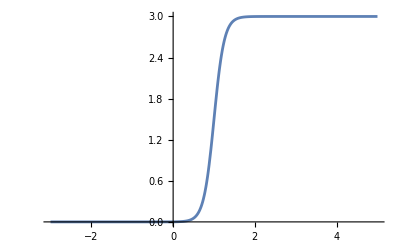

```mathematica
Plot[Sform'[t]/Sform[t]//.{H->3,Om->4,tstar->1},{t,-3,5}]
```

### Write out coefficients

```mathematica
(*---2. Variable names to unpack from struct---*)
variables={"Phi","S","Sdot","Phidot","A","PhiZ","SZ","SdotZ","PhidotZ","AZ","PhiZZ","SZZ","SdotZZ","PhidotZZ","AZZ","z","LN","t","X","p2","a4","DS0","DS1","DS2","DS3","DS4"};

(*---3. Field names and coefficient labels---*)
fields={"Phi","S","Sdot","Phidot","A"};
coeffLabels={"Coeff0","Coeff1","Coeff2","Src"};
```

```mathematica
makeJuliaFuncBdry[field_,label_,expr_,exprB_]:=Module[{fname},fname=field<>label;
"function "<>fname<>"(v::PDEVars{T}) where {T}\n\n"<>"    @unpack "<>StringRiffle[variables,", "]<>" = v\n\n"<>"if z == 0 \n co = "<>ToJuliaForm[ToString[InputForm[exprB]]]
<>";\n else \n    co = "<>ToJuliaForm[ToString[InputForm[expr]]]<>";\nend\n\n
"<>"    return co\nend\n\n"];
```

```mathematica
(*---1. Julia-compatible symbolic conversion---*)
ToJuliaForm[expr_]:=Module[{s},s=ToString[expr//FortranForm];
s=StringReplace[s,{"Sin["->"sin(","Sinh["->"sinh(","Cos["->"cos(","Cosh["->"cosh(","Tan["->"tan(","Tanh["->"tanh(","Sech["->"sech(","Exp["->"exp(","Log["->"log(","Sqrt["->"sqrt(","Vfun["->"Vfun(","Derivative[1][Vfun]["->"DV(","]"->")","\""->"","**"->"^"}];
s];
```

```mathematica
cosmocoeffs={SCoeffs,SdotCoeffs,PhidotCoeffs,ACoeffs};
cosmocoeffsB={SCoeffsB,SdotCoeffsB,PhidotCoeffsB,ACoeffsB};
```

```mathematica
str=strStart;

For[var=1,var<=4,var++,
field=fields[[var+1]];
For[ii=1,ii<4,ii++,
label=coeffLabels[[ii]];
str=str<>makeJuliaFuncBdry[field,label,(cosmocoeffs[[var,ii+1]]//.replfun//.replDS0),cosmocoeffsB[[var,ii+1]]//.replfun//.replDS0];
];
label=coeffLabels[[4]];
str=str<>makeJuliaFuncBdry[field,label,(cosmocoeffs[[var,1]]//.replfun//.replDS0),cosmocoeffsB[[var,1]]//.replfun//.replDS0];
];
```

```mathematica
str=StringReplace[str,".*" ->"."<>" "<>"*"];
```

```mathematica
strfile=OpenWrite["/Users/jankozuszek/Documents/Holography with dynamic boundary/Reproducing-Dynamic-Holo/Equation expressions/ODECoeffExpr.jl"];
WriteString[strfile,str];
Close[strfile];
```

```mathematica
str
```

```mathematica
str=strStart;
For[ii = 0, ii<=6,ii++,
str=str<>"function DS"<>ToString[ii]<>"f(t)\n\n";
str=str<>"res = "<>ToString[Simplify[D[Sform[t],{t,ii}]]//ToJuliaForm]<>"; \n\n";
str=str<>"return res;\nend\n\n";
];
```

```mathematica
str=StringReplace[str,".*" ->"."<>" "<>"*"];
```

```mathematica
(*strfile=OpenWrite["/Users/jankozuszek/Documents/Holography with dynamic boundary/Reproducing-Dynamic-Holo/Equation expressions/CosmoS0Expr.jl"];
WriteString[strfile,str];
Close[strfile];*)
```

## Time step

### General

```mathematica
Clear[S0]
```

```mathematica
stepeq=(Subscript[Φfun, d][r,t]-(D[Φfun[r,t],t]+1/2 Afun[r,t]D[Φfun[r,t],r]))//.D[replWithSub,t]//.replWithSub//.RtoZ//Simplify;
```

```mathematica
solTimeStep=Solve[0==stepeq,  Derivative[0,1][PhiSub][z,t]][[1]]//Expand//Simplify;
```

We need ξ’[t] here. We get it by demanding that the apparent horizon stay in the same spot. To that end, we demand ∂_t Ṡ(z_AH,t)=0 and we take z_AH=1/2. This requires solving  0=1/2 A Ṡ'+2/3 S (Φ̇)^2-1/2 Ṡ A'.

```mathematica
solconstr=Solve[0==constrEq//.{Subscript[Sfun, dd][r,t]->(D[Subscript[Sfun, d][r,t],t]+1/2 Afun[r,t]D[Subscript[Sfun, d][r,t],r])},Derivative[0,1][Subscript[Sfun, d]][r,t]][[1]]//Simplify//Expand
```

{Sfun_d^(0,1)[r,t]→-2/3 Sfun[r,t] Φfun_d[r,t]^2+1/2 Sfun_d[r,t] Afun^(1,0)[r,t]-1/2 Afun[r,t] Sfun_d^(1,0)[r,t]}

```mathematica
Solve[0==Subscript[Sfun, d][r,t]//.replWithSub//.{S0->(1&)}//.RtoZ,ξ[t]]//.toODE//.{z->1/2}//Simplify
```

{{ξ[t]→-2-(√(2 M^2-3 SdotSub[1/2]))/(√6)},{ξ[t]→-2+(√(2 M^2-3 SdotSub[1/2]))/(√6)}}

```mathematica
XiPrimeExpr=(Derivative[0,1][Subscript[Sfun, d]][r,t]//.solconstr)+DConst Subscript[Sfun, d][r,t];
```

```mathematica
XiPrimeExprAH=XiPrimeExpr//.replWithSub//.RtoZ//Simplify;
```

```mathematica
solXiPrime=Solve[0==XiPrimeExprAH,ξ'[t]][[1]]//Expand//Simplify;
```

```mathematica
XiPrimeStr=ξ'[t]//.solXiPrime//.toODE//.replfun//.replDS0//ToJuliaForm;
```

```mathematica
DtPhiStr=Derivative[0,1][PhiSub][z,t]//.solTimeStep//.toODE//.replfun//.replDS0//.{ξ'[t]->XPrime}//ToJuliaForm;
```

```mathematica
DtPhiB=SeriesCoefficient[Derivative[0,1][PhiSub][z,t]//.solTimeStep//.toODE,{z,0,0}]//.{PhiSub[0]->Subscript[p, 2][t],PhidotSub[0]->-PhidotCoeffsB[[1]]/PhidotCoeffsB[[2]]}//Simplify
```

(-6 M S0'[t]^3+4 S0[t]^3 (-3 M ξ[t]^3+3 (PhidotSub'[0]+2 PhiSub'[0])+ξ[t] (2 M^3+9 p_2[t]+6 M ξ'[t]))+3 M S0[t] S0'[t] (-5 ξ[t] S0'[t]+S0''[t])+3 M S0[t]^2 (7 ξ[t] S0''[t]+S0^(3)[t]))/(12 S0[t]^3)

```mathematica
DtPhiBStr=DtPhiB//.{PhidotSub'[0]->PhidotZ,PhiSub'[0]->PhiZ,ξ'[t]->XPrime}//.replfun//.replDS0//ToJuliaForm//ToString;
```

```mathematica
a4PrimeStr=Subscript[a, 4]'[t]//.sola4//.toODE//.replfun//.replDS0//.{ξ'[t]->XPrime,Subscript[p, 2]'[t]->p2Prime}//ToJuliaForm
```

(2*((9*DS1*DS2*M^2)/DS0^2 + (2*(6*DS3*M^2 + DS1*(-27*a4 + 4*M^4 - 18*M*p2)))/DS0 - 18*M*p2Prime + (36*DS1*M^2*X^2)/DS0 + 36*M^2*X*XPrime))/27

```mathematica
str=strStart;
```

```mathematica
str=str<>"function DtX(v::PDEVars{T}) where {T}\n\n"<>"    @unpack "<>StringRiffle[variables,", "]<>" = v\n\n";
str=str<>"XPrime = "<>ToString[XiPrimeStr]<>";\n\n return XPrime\nend\n\n";
```

```mathematica
str=str<>"function DtPhi(XPrime, v::PDEVars{T}) where {T}\n\n"<>"    @unpack "<>StringRiffle[variables,", "]<>" = v\n\nif z == 0\n";
str=str<>"PhiT = "<>DtPhiBStr<>";\nelse\n"; 
str=str<>"PhiT = "<>ToString[DtPhiStr]<>";\nend\n\n return PhiT\nend\n\n";
```

```mathematica
str=str<>"function Dta4(params, DSvals, XPrime, p2Prime)\n\n t, X, p2, a4 = params;\n DS0, DS1, DS2, DS3, DS4 = DSvals;\n\n";
str= str<>"a4Prime = "<>ToString[a4PrimeStr]<>";\n\n";
str=str<>"return a4Prime;\nend;\n\n";
```

```mathematica
str=StringReplace[str,".*" ->"."<>" "<>"*"];
```

```mathematica
(*strfile=OpenWrite["/Users/jankozuszek/Documents/Holography with dynamic boundary/Reproducing-Dynamic-Holo/Equation expressions/CosmoTimeStepExpr.jl"];
WriteString[strfile,str];
Close[strfile];*)
```

## Constraint equation

```mathematica
constrEq
```

Sfun_dd[r,t]+2/3 Sfun[r,t] Φfun_d[r,t]^2-1/2 Sfun_d[r,t] Afun^(1,0)[r,t]

```mathematica
constrEq=constrEq//.{Subscript[Sfun, dd][r,t]->(D[Subscript[Sfun, d][r,t],t]+1/2 Afun[r,t]D[Subscript[Sfun, d][r,t],r])}
```

2/3 Sfun[r,t] Φfun_d[r,t]^2+Sfun_d^(0,1)[r,t]-1/2 Sfun_d[r,t] Afun^(1,0)[r,t]+1/2 Afun[r,t] Sfun_d^(1,0)[r,t]

```mathematica
tmp=constrEq//.replWithSub//.D[replWithSub,t]//.D[replWithSub,r]//Simplify;
```

```mathematica
constrStr=Simplify[tmp//.RtoZ]//.{Derivative[0,1][SdotSub][z,t]->DtSdotSub[z]}//.toODE//.replDS0//.{ξ'[t]->XPrime};
```

```mathematica
Series[constrStr,{z,0,1}]
```

((-9 DS1^2 M^2-25 DS0 DS2 M^2-4 DS0^2 M^4+72 DS0^2 ASub[0]-48 DS0^2 M PhidotSub[0]-144 DS0 SdotSub[0]+32 DS0 DS1 M^2 ξ[t]) z)/(72 DS0)+O[z]^2

```mathematica
str=strStart;
str="function constr(SdotT, XPrime, v::PDEVars{T}) where {T}\n\n  @unpack "<>StringRiffle[variables,", "]<>" = v\n\n";
str=str<>"res = "<>ToString[constrStr//.replfun//.replDS0//.{ξ'[t]->XPrime,DtSdotSub[z]->SdotT}//ToJuliaForm]<>";\n\n";
str=str<>"return res\nend\n\n";
```

```mathematica
str=StringReplace[str,".*" ->"."<>" "<>"*"];
```

```mathematica
str
```

function constr(SdotT, XPrime, v::PDEVars{T}) where {T}

  @unpack Phi, S, Sdot, Phidot, A, PhiZ, SZ, SdotZ, PhidotZ, AZ, PhiZZ, SZZ, SdotZZ, PhidotZZ, AZZ, z, LN, t, X, p2, a4, DS0, DS1, DS2, DS3, DS4 = v

res = (-1440*DS0^6*DS1*z*(30*DS1^3*LN*M^2*z^5 + 30*DS0^3*(3 + 6*X*z - M^2*z^2 + 3*X^2*z^2) + 9*DS0*DS1*z^2*(-6*DS2*LN*M^2*z^3 + 5*DS1*(2 - LN*M^2*z^2 + 2*LN*M^2*X*z^3)) + DS0^2*z*(180*Sdot*z^3 + 20*DS1*(9 + 9*X*z - 2*M^2*z^2) + 3*LN*M^2*z^3*(4*DS3*z + DS2*(5 - 10*X*z)))) + 120*DS0^5*(DS1*DS2*(1 - 3*LN)*M^2*z^5 + 3*DS0^2*(-2 - 2*X*z + 2*A*z^4 + AZ*z^5) + DS0*M^2*z^4*(DS3*(-1 + 3*LN)*z + DS2*(-2 + 4*LN + 4*(1 - 3*LN)*X*z)))*(30*DS1^3*LN*M^2*z^5 + 30*DS0^3*(3 + 6*X*z - M^2*z^2 + 3*X^2*z^2) + 9*DS0*DS1*z^2*(-6*DS2*LN*M^2*z^3 + 5*DS1*(2 - LN*M^2*z^2 + 2*LN*M^2*X*z^3)) + DS0^2*z*(180*Sdot*z^3 + 20*DS1*(9 + 9*X*z - 2*M^2*z^2) + 3*LN*M^2*z^3*(4*DS3*z + DS2*(5 - 10*X*z)))) + 120*DS0^5*(DS1*z^2*(3*DS1 - DS2*LN*M^2*z^3) + DS0^2*(3 + 6*X*z - 2*M^2*z^2 + 3*X^2*z^2 - 6*XPrime*z^2 + 3*A*z^4) + DS0*(DS3*LN*M^2*z^5 + DS2*(-6*z^2 + 2*LN*M^2*z^4 - 4*LN*M^2*X*z^5)))*(30*DS1^3*(1 - 3*LN)*M^2*z^5 + 180*DS0^3*(1 + X*z) - 9*DS0*DS1*M^2*z^4*(6*DS2*(1 - 3*LN)*z + 5*DS1*(1 - 2*LN + 2*(-1 + 3*LN)*X*z)) - DS0^2*z*(360*Sdot*z^3 - 20*DS1*(9 + 2*M^2*z^2) + 3*z^3*(4*(DS3*(-1 + 3*LN)*M^2 + 15*SdotZ)*z - 5*DS2*M^2*(1 - 2*LN + 2*(-1 + 3*LN)*X*z)))) + 720*DS0^7*z*(180*DS0^3*XPrime*z*(1 + X*z) + 9*DS1^2*z^2*(4*DS2*LN*M^2*z^3 + 5*DS1*(2 - LN*M^2*z^2 + 2*LN*M^2*X*z^3)) + DS0^2*(90*DS1*(3 + 6*X*z - M^2*z^2 + 3*X^2*z^2 + 2*XPrime*z^2) + 10*DS2*z*(18 + 18*X*z - 4*M^2*z^2 - 3*LN*M^2*XPrime*z^4) + 3*z^4*(60*SdotT + 4*DS4*LN*M^2*z + 5*DS3*LN*M^2*(1 - 2*X*z))) + 2*DS0*z*(180*DS1*Sdot*z^3 - 27*DS2^2*LN*M^2*z^4 + 5*DS1^2*(36 + 36*X*z - 8*M^2*z^2 + 9*LN*M^2*XPrime*z^4) + 15*DS1*z*(-(DS3*LN*M^2*z^3) + DS2*(6 - 2*LN*M^2*z^2 + 4*LN*M^2*X*z^3)))) + (4*DS1^3*LN*M*z^4 + 2*DS0^3*z*(M - 2*Phidot*z^2) + DS0*DS1*LN*M*z^3*(-2*DS2*z + DS1*(-3 + 6*X*z)) + DS0^2*LN*M*z^3*(-2*DS3*z + DS2*(-3 + 6*X*z)))^2*(3*DS1^4*(199 - 90*LN)*LN*M^2*z^6 - 9*DS0*DS1^2*LN*M^2*z^5*(3*DS2*(53 + 20*LN)*z + 100*DS1*(1 - 4*X*z)) + 1800*DS0^4*(3 - M^2*z^2 + X*z*(3 + M^2*z^2)) + DS0^2*LN*M*z^4*(6*DS2^2*(247 - 45*LN)*M*z^2 + 20*DS1^2*(45*M - 135*M*X*z + 23*M^3*z^2 + 54*p2*z^2 + 216*M*X^2*z^2) + 15*DS1*M*z*(47*DS3*z + 84*DS2*(1 - 4*X*z))) + 5*DS0^3*z*(1080*S*z^3 - 120*DS1*(-9 + M^2*z^2) + LN*M*z^3*(4*DS2*(45*M - 135*M*X*z + 28*M^3*z^2 + 54*p2*z^2 + 216*M*X^2*z^2) + 3*M*z*(25*DS4*z - 48*DS3*(-1 + 4*X*z))))))/(129600. *DS0^9*z^3);

return res
end

```mathematica
strfile=OpenWrite["/Users/jankozuszek/Documents/Holography with dynamic boundary/Reproducing-Dynamic-Holo/Equation expressions/CosmoConstrExpr.jl"];
WriteString[strfile,str];
Close[strfile];
```

```mathematica
DSolve[f'[t]==-D f[t],f,t]
```

{{f→Function[{t},ⅇ^(-D t) C[1]]}}

## Friedmann equation on the boundary: Solving for S0^(n)

```mathematica
eps
```

(7 M^4)/36-M^4 β+M^2 ξ[t]^2-(3 a_4[t])/4-M p_2[t]-(M^2 S0'[t]^2)/(4 S0[t]^2)+(3 S0'[t]^4)/(16 S0[t]^4)+(M^2 S0''[t])/(4 S0[t])

```mathematica
mom
```

(4 S0[t]^4 (-5 M^4+108 M^4 β-36 M^2 ξ[t]^2-27 a_4[t]+36 M p_2[t])+144 M^2 S0[t]^2 S0'[t]^2+27 S0'[t]^4+24 M^2 S0[t]^3 S0''[t]-108 S0[t] S0'[t]^2 S0''[t])/(432 S0[t]^4)

```mathematica
Eps[t_]:=-(3 Subscript[a, 4][t])/4-M Subscript[p, 2][t]+(3 S0'[t]^4)/(16 S0[t]^4)+M^2(ξ[t]^2+S0'[t]^2/(8 S0[t]^2)+(2S0''[t])/(3S0[t]))-M^4(β-7/36);
```

```mathematica
Mom[t_]:=(-Subscript[a, 4][t])/4+1/3 M Subscript[p, 2][t]+(S0'[t]^2(S0'[t]^2-4S0[t]S0''[t]))/(16 S0[t]^4)-M^2/3(ξ[t]^2+S0'[t]^2/(8 S0[t]^2)+(13S0''[t])/(12S0[t]))+M^4(β-5/108);
```

```mathematica
(*Eps[t_]:=(7 M^4)/36-M^4 β+M^2 ξ[t]^2-(3 Subscript[a, 4][t])/4-M Subscript[p, 2][t]-(M^2 S0'[t]^2)/(4 S0[t]^2)+(3 S0'[t]^4)/(16 S0[t]^4)+(M^2 S0''[t])/(4 S0[t]);
Mom[t_]:=(4 S0[t]^4 (-5 M^4+108 M^4 β-36 M^2 ξ[t]^2-27 Subscript[a, 4][t]+36 M Subscript[p, 2][t])+144 M^2 S0[t]^2 S0'[t]^2+27 S0'[t]^4+24 M^2 S0[t]^3 S0''[t]-108 S0[t] S0'[t]^2 S0''[t])/(432 S0[t]^4);*)
```

```mathematica
FriedEq1=Simplify[(S0'[t]/S0[t])^2-(1/3 Λ+(8 Subscript[G, N])/3 Eps[t])];
FriedEq2=Simplify[3 S0''[t]/S0[t]-(Λ-4 Subscript[G, N](Eps[t]+3Mom[t]))];
ContEq=Simplify[(D[Eps[t],t])+3(S0'[t]/S0[t])(Eps[t]+Mom[t])];
```

```mathematica
ContEq//.sola4//Simplify
```

0

```mathematica
Solve[0==FriedEq2,S0''[t]][[1]]//Simplify
```

{S0''[t]→(-2 S0[t]^4 (9 Λ-2 G_N (M^4+36 M^4 β-27 a_4[t]))+27 G_N S0'[t]^4)/(6 (S0[t]^3 (-9+5 M^2 G_N)+9 S0[t] G_N S0'[t]^2))}

```mathematica
solS02=Solve[0==FriedEq1,S0''[t]][[1]]//Simplify
```

{S0''[t]→-(2 S0[t]^4 (9 Λ-2 G_N (-7 M^4+36 M^4 β-36 M^2 ξ[t]^2+27 a_4[t]+36 M p_2[t]))+18 S0[t]^2 (-3+M^2 G_N) S0'[t]^2+27 G_N S0'[t]^4)/(96 M^2 S0[t]^3 G_N)}

```mathematica
tmp=FriedEq2//.solS02//Simplify
```

1/(96 M^2 S0[t]^6 G_N)(S0[t]^6 (-54 Λ+4 M^2 G_N^2 (17 M^4+132 M^4 β+60 M^2 ξ[t]^2-189 a_4[t]-60 M p_2[t])+6 G_N (-14 M^4+72 M^4 β-11 M^2 Λ-72 M^2 ξ[t]^2+54 a_4[t]+72 M p_2[t]))-6 S0[t]^4 (-27+3 (8 M^2-3 Λ) G_N+G_N^2 (-19 M^4+72 M^4 β-72 M^2 ξ[t]^2+54 a_4[t]+72 M p_2[t])) S0'[t]^2+243 S0[t]^2 G_N (-1+M^2 G_N) S0'[t]^4+81 G_N^2 S0'[t]^6)

```mathematica
coefsS01 = CoefficientList[tmp,S0'[t]]//Simplify
```

{1/48 (-(27 Λ)/(M^2 G_N)+3 (-14 M^2+72 M^2 β-11 Λ-72 ξ[t]^2+(54 a_4[t])/M^2+(72 p_2[t])/M)+2 G_N (17 M^4+132 M^4 β+60 M^2 ξ[t]^2-189 a_4[t]-60 M p_2[t])),0,(27+(-24 M^2+9 Λ) G_N+G_N^2 (19 M^4-72 M^4 β+72 M^2 ξ[t]^2-54 a_4[t]-72 M p_2[t]))/(16 M^2 S0[t]^2 G_N),0,(81 (-1+M^2 G_N))/(32 M^2 S0[t]^4),0,(27 G_N)/(32 M^2 S0[t]^6)}

```mathematica
coefsS01//Length
```

7

We can determine further derivatives of the scale factor in terms of the expansion parameters of Φ, using the boundary Einstein equations to eliminate time derivatives of p_2.

```mathematica
solp2dt=Solve[0==D[FriedEq2,t]//.solS02//.sola4,Subscript[p, 2]'[t]][[1]]//Simplify;
```

```mathematica
solS03=Solve[Subscript[p, 3][t]==(Subscript[p, 3][t]//.ASPsol//.Join[solp2dt,solS02]//Simplify), Derivative[3][S0][t]][[1]]//Simplify
```

{S0^(3)[t]→(384 M^4 S0[t]^9 G_N (-264 M^2 G_N ξ[t]^3+ξ[t] (-9 Λ+2 G_N (M^4 (-7+36 β)+27 a_4[t]+180 M p_2[t]))+96 M G_N p_3[t])-4 S0[t]^8 (81 Λ (-8 M^2+3 Λ)+36 G_N (-28 M^6+144 M^6 β-25 M^4 Λ-108 M^4 β Λ-36 (4 M^4-3 M^2 Λ) ξ[t]^2+27 (4 M^2-3 Λ) a_4[t]+144 M^3 p_2[t]-108 M Λ p_2[t])+4 G_N^2 (527 M^8+1800 M^8 β+3888 M^8 β^2+3888 M^4 ξ[t]^4+2187 a_4[t]^2-2808 M^5 p_2[t]+7776 M^5 β p_2[t]+3888 M^2 p_2[t]^2-216 M^2 ξ[t]^2 (M^4 (-13+36 β)+27 a_4[t]+36 M p_2[t])+54 a_4[t] (M^4 (-103+108 β)+108 M p_2[t]))) S0'[t]+1152 M^4 S0[t]^7 G_N (9+13 M^2 G_N) ξ[t] S0'[t]^2+24 S0[t]^6 (81 (-4 M^2+3 Λ)-9 G_N (38 M^4+216 M^4 β+69 M^2 Λ-216 M^2 ξ[t]^2+162 a_4[t]+216 M p_2[t])+2 M^2 G_N^2 (-89 M^4+2484 M^4 β-2484 M^2 ξ[t]^2+1863 a_4[t]+2484 M p_2[t])) S0'[t]^3-5184 M^4 S0[t]^5 G_N^2 ξ[t] S0'[t]^4+108 S0[t]^4 (-81+9 (50 M^2-3 Λ) G_N+G_N^2 (-335 M^4+216 M^4 β-216 M^2 ξ[t]^2+162 a_4[t]+216 M p_2[t])) S0'[t]^5-972 S0[t]^2 G_N (-9+23 M^2 G_N) S0'[t]^7-2187 G_N^2 S0'[t]^9)/(1536 M^4 S0[t]^6 G_N (S0[t]^2 (-9+13 M^2 G_N)+9 G_N S0'[t]^2))}

```mathematica
solp2dt2=D[solp2dt,t]//Simplify
```

{p_2''[t]→1/(12288 M^5 S0[t]^10 G_N^2)(540 S0[t]^4 (-27+3 (50 M^2-3 Λ) G_N+G_N^2 (-149 M^4+72 M^4 β-72 M^2 ξ[t]^2+54 a_4[t]+72 M p_2[t])) S0'[t]^6-2268 S0[t]^2 G_N (-9+23 M^2 G_N) S0'[t]^8-6561 G_N^2 S0'[t]^10+2268 S0[t]^3 G_N (-9+23 M^2 G_N) S0'[t]^6 S0''[t]+6561 S0[t] G_N^2 S0'[t]^8 S0''[t]-108 S0[t]^5 S0'[t]^4 (-135 S0''[t]+15 (50 M^2-3 Λ) G_N S0''[t]+G_N^2 (-144 M^2 ξ[t] S0'[t] ξ'[t]+18 S0'[t] (3 a_4'[t]+4 M p_2'[t])-360 M^2 ξ[t]^2 S0''[t]+5 (M^4 (-149+72 β)+54 a_4[t]+72 M p_2[t]) S0''[t]))+24576 M^6 S0[t]^10 G_N^2 (ξ'[t]^2+ξ[t] ξ''[t])+216 S0[t]^6 S0'[t]^3 ((-36 M^2+27 Λ+6 M^2 G_N^2 (-19 M^4+92 M^4 β-92 M^2 ξ[t]^2+69 a_4[t]+92 M p_2[t])-G_N (-74 M^4+216 M^4 β+69 M^2 Λ-216 M^2 ξ[t]^2+162 a_4[t]+216 M p_2[t])) S0'[t]-64 M^4 G_N^2 S0^(3)[t])-4 S0[t]^8 ((27 Λ (-8 M^2+3 Λ)+12 G_N (-28 M^6+144 M^6 β+31 M^4 Λ-108 M^4 β Λ-36 (4 M^4-3 M^2 Λ) ξ[t]^2+27 (4 M^2-3 Λ) a_4[t]+144 M^3 p_2[t]-108 M Λ p_2[t])+4 G_N^2 (437 M^8-744 M^8 β+1296 M^8 β^2+1296 M^4 ξ[t]^4+729 a_4[t]^2-2280 M^5 p_2[t]+2592 M^5 β p_2[t]+1296 M^2 p_2[t]^2+54 a_4[t] (M^4 (-53+36 β)+36 M p_2[t])-24 M^2 ξ[t]^2 (M^4 (-95+108 β)+81 a_4[t]+108 M p_2[t]))) S0'[t]^2-1536 M^6 G_N^2 S0''[t]^2+1152 M^4 G_N (-1+M^2 G_N) S0'[t] S0^(3)[t])+4 S0[t]^9 (27 Λ (-8 M^2+3 Λ) S0''[t]+12 G_N (-72 M^2 (4 M^2-3 Λ) ξ[t] S0'[t] ξ'[t]+9 (4 M^2-3 Λ) S0'[t] (3 a_4'[t]+4 M p_2'[t])-28 M^6 S0''[t]+144 M^6 β S0''[t]+31 M^4 Λ S0''[t]-108 M^4 β Λ S0''[t]-36 M^2 (4 M^2-3 Λ) ξ[t]^2 S0''[t]+108 M^2 a_4[t] S0''[t]-81 Λ a_4[t] S0''[t]+144 M^3 p_2[t] S0''[t]-108 M Λ p_2[t] S0''[t]-96 M^4 S0^(4)[t])+4 G_N^2 (5184 M^4 ξ[t]^3 S0'[t] ξ'[t]-48 M^2 ξ[t] (M^4 (-95+108 β)+81 a_4[t]+108 M p_2[t]) S0'[t] ξ'[t]+6 S0'[t] (9 (M^4 (-53+36 β)+27 a_4[t]+36 M p_2[t]) a_4'[t]+4 M (M^4 (-95+108 β)+81 a_4[t]+108 M p_2[t]) p_2'[t])+437 M^8 S0''[t]-744 M^8 β S0''[t]+1296 M^8 β^2 S0''[t]+1296 M^4 ξ[t]^4 S0''[t]-2862 M^4 a_4[t] S0''[t]+1944 M^4 β a_4[t] S0''[t]+729 a_4[t]^2 S0''[t]-2280 M^5 p_2[t] S0''[t]+2592 M^5 β p_2[t] S0''[t]+1944 M a_4[t] p_2[t] S0''[t]+1296 M^2 p_2[t]^2 S0''[t]-24 M^2 ξ[t]^2 (27 S0'[t] (3 a_4'[t]+4 M p_2'[t])+(M^4 (-95+108 β)+81 a_4[t]+108 M p_2[t]) S0''[t])+672 M^6 S0^(4)[t]))+24 S0[t]^7 S0'[t] (81 (4 M^2-3 Λ) S0'[t] S0''[t]+9 G_N S0'[t] (-144 M^2 ξ[t] S0'[t] ξ'[t]+18 S0'[t] (3 a_4'[t]+4 M p_2'[t])-216 M^2 ξ[t]^2 S0''[t]+(-74 M^4+216 M^4 β+69 M^2 Λ+162 a_4[t]+216 M p_2[t]) S0''[t])-2 M^2 G_N^2 (-1656 M^2 ξ[t] S0'[t]^2 ξ'[t]+207 S0'[t]^2 (3 a_4'[t]+4 M p_2'[t])-2484 M^2 ξ[t]^2 S0'[t] S0''[t]-192 M^2 S0''[t] S0^(3)[t]+S0'[t] ((M^4 (-257+2484 β)+1863 a_4[t]+2484 M p_2[t]) S0''[t]-96 M^2 S0^(4)[t]))))}

```mathematica
solS04=Solve[Subscript[p, 4][t]==(Subscript[p, 4][t]//.ASPsol//.Join[solp2dt,solp2dt2,solS03,solS02,sola4]//Simplify),Derivative[4][S0][t]][[1]]//Simplify;
```

```mathematica
DS2expr=Derivative[2][S0][t]//.solS02//.replfun//.replDS0//.{Subscript[G, N]->GBd,Λ->LBd,β->beta}//ToJuliaForm;
```

```mathematica
DS3expr=Derivative[3][S0][t]//.solS03//.replfun//.replDS0//.{Subscript[p, 3][t]->p3,Subscript[G, N]->GBd,Λ->LBd,β->beta}//ToJuliaForm;
```

```mathematica
DS4expr=Derivative[4][S0][t]//.solS04//.replfun//.replDS0//.{Subscript[p, 3][t]->p3,Subscript[p, 4][t]->p4,Subscript[G, N]->GBd,Λ->LBd,β->beta}//ToJuliaForm;
```

```mathematica
DSexprlist={DS2expr,DS3expr,DS4expr};
```

```mathematica
DtDS1expr=Simplify[S0''[t]//.Solve[0==D[tmp,t],S0''[t]][[1]]]//.replfun//.replDS0//.{Subscript[G, N]->GBd,Λ->LBd,β->beta,Subscript[p, 2]'[t]->p2Prime,ξ'[t]->XPrime,Subscript[a, 4]'[t]->a4Prime}//ToJuliaForm
```

(-81*DS1^7*GBd^2 - 162*DS0^2*DS1^5*GBd*(-1 + GBd*M^2) + 2*DS0^4*DS1^3*(-27 + 3*GBd*(-3*LBd + 8*M^2) + GBd^2*(54*a4 - 19*M^4 + 72*beta*M^4 + 72*M*p2 - 72*M^2*X^2)) + 18*DS0^5*DS1^2*GBd^2*(-3*a4Prime - 4*M*p2Prime + 8*M^2*X*XPrime) + 2*DS0^7*GBd*(-9*a4Prime*(-3 + 7*GBd*M^2) + 4*M*(9 - 5*GBd*M^2)*p2Prime + 8*M^2*(-9 + 5*GBd*M^2)*X*XPrime))/(-81*DS0*DS1^5*GBd^2 - 162*DS0^3*DS1^3*GBd*(-1 + GBd*M^2) + 2*DS0^5*DS1*(-27 + 3*GBd*(-3*LBd + 8*M^2) + GBd^2*(54*a4 - 19*M^4 + 72*beta*M^4 + 72*M*p2 - 72*M^2*X^2)))

```mathematica
str=strStart;
str=str<>"function DS1f(params)\n\n t, X, p2, a4, DS0 = params;\n";
str=str<>Table["co"<>ToString[ii]<>" = "<>ToString[coefsS01[[2*ii+1]]//.replfun//.replDS0//.{Subscript[G, N]->GBd,Λ->LBd,β->beta}//ToJuliaForm]<>";\n",{ii,0,3}];
str=str<>"\nDS1eq = poly.Polynomial([co0,co1,co2,co3]);\n\n candidates = poly.roots(DS1eq);\n\n";
str=str<>"real_and_positive = [real(r) for r in candidates if (abs(imag(r))<1.e-8 && real(r)>0)]; \nsort!(real_and_positive);\n\n";
str=str<>"return sqrt(real_and_positive[1]) \nend\n\n";
```

```mathematica
For[ii=2,ii<=4,ii++,
str=str<>"function DS"<>ToString[ii]<>"f(params, p3, p4)\n\n t, X, p2, a4, DS0, DS1 = params;\n";
str=str<>"val = "<>ToString[DSexprlist[[ii-1]]]<>";\n\nreturn val\nend\n\n";]
```

```mathematica
str=str<>"function DtDS1f(params, XPrime, p2Prime, a4Prime)\n\n t, X, p2, a4, DS0, DS1 = params;\n";
str=str<>"val = "<>ToString[DtDS1expr]<>";\n\nreturn val\nend\n\n";
```

```mathematica
str
```

# ==============================================
#  Auto-generated Julia code from Mathematica
#  Do not edit manually
# ==============================================


# ----------------------------------------------
#  Generated functions
# ----------------------------------------------

function DS1f(params)

 t, X, p2, a4, DS0 = params;
co0 = ((-27*LBd)/(GBd*M^2) + 3*(-11*LBd + (54*a4)/M^2 - 14*M^2 + 72*beta*M^2 + (72*p2)/M - 72*X^2) + 2*GBd*(-189*a4 + 17*M^4 + 132*beta*M^4 - 60*M*p2 + 60*M^2*X^2))/48;
co1 = (27 + GBd*(9*LBd - 24*M^2) + GBd^2*(-54*a4 + 19*M^4 - 72*beta*M^4 - 72*M*p2 + 72*M^2*X^2))/(16*DS0^2*GBd*M^2);
co2 = (81*(-1 + GBd*M^2))/(32*DS0^4*M^2);
co3 = (27*GBd)/(32*DS0^6*M^2);

DS1eq = poly.Polynomial([co0,co1,co2,co3]);

 candidates = poly.roots(DS1eq);

real_and_positive = [real(r) for r in candidates if (abs(imag(r))<1.e-8 && real(r)>0)]; 
sort!(real_and_positive);

return sqrt(real_and_positive[1]) 
end

function DS2f(params, p3, p4)

 t, X, p2, a4, DS0, DS1 = params;
val = -1/96*(27*DS1^4*GBd + 18*DS0^2*DS1^2*(-3 + GBd*M^2) + 2*DS0^4*(9*LBd - 2*GBd*(27*a4 - 7*M^4 + 36*beta*M^4 + 36*M*p2 - 36*M^2*X^2)))/(DS0^3*GBd*M^2);

return val
end

function DS3f(params, p3, p4)

 t, X, p2, a4, DS0, DS1 = params;
val = (-2187*DS1^9*GBd^2 - 972*DS0^2*DS1^7*GBd*(-9 + 23*GBd*M^2) - 5184*DS0^5*DS1^4*GBd^2*M^4*X + 1152*DS0^7*DS1^2*GBd*M^4*(9 + 13*GBd*M^2)*X + 384*DS0^9*GBd*M^4*(96*GBd*M*p3 + (-9*LBd + 2*GBd*(27*a4 + (-7 + 36*beta)*M^4 + 180*M*p2))*X - 264*GBd*M^2*X^3) + 108*DS0^4*DS1^5*(-81 + 9*GBd*(-3*LBd + 50*M^2) + GBd^2*(162*a4 - 335*M^4 + 216*beta*M^4 + 216*M*p2 - 216*M^2*X^2)) + 24*DS0^6*DS1^3*(81*(3*LBd - 4*M^2) + 2*GBd^2*M^2*(1863*a4 - 89*M^4 + 2484*beta*M^4 + 2484*M*p2 - 2484*M^2*X^2) - 9*GBd*(162*a4 + 69*LBd*M^2 + 38*M^4 + 216*beta*M^4 + 216*M*p2 - 216*M^2*X^2)) - 4*DS0^8*DS1*(81*LBd*(3*LBd - 8*M^2) + 36*GBd*(-25*LBd*M^4 - 108*beta*LBd*M^4 - 28*M^6 + 144*beta*M^6 + 27*a4*(-3*LBd + 4*M^2) - 108*LBd*M*p2 + 144*M^3*p2 - 36*(-3*LBd*M^2 + 4*M^4)*X^2) + 4*GBd^2*(2187*a4^2 + 527*M^8 + 1800*beta*M^8 + 3888*beta^2*M^8 - 2808*M^5*p2 + 7776*beta*M^5*p2 + 3888*M^2*p2^2 + 54*a4*((-103 + 108*beta)*M^4 + 108*M*p2) - 216*M^2*(27*a4 + (-13 + 36*beta)*M^4 + 36*M*p2)*X^2 + 3888*M^4*X^4)))/(1536*DS0^6*GBd*M^4*(9*DS1^2*GBd + DS0^2*(-9 + 13*GBd*M^2)));

return val
end

function DS4f(params, p3, p4)

 t, X, p2, a4, DS0, DS1 = params;
val = (-7971615*DS1^14*GBd^4 + 295245*DS0^2*DS1^12*GBd^3*(171 - 211*GBd*M^2) - 268738560*DS0^9*DS1^5*GBd^4*M^5*p3 - 11943936*DS0^13*DS1*GBd^3*M^5*(15*LBd + 8*M^2)*p3 + 35831808*DS0^11*DS1^3*GBd^3*M^5*(15 - 29*GBd*M^2)*p3 + 2654208*DS0^13*DS1*GBd^4*M^5*(405*a4 + (-137 + 540*beta)*M^4 + 540*M*p2)*p3 - 28311552*DS0^12*GBd^3*M^7*(9*DS1^2*GBd + DS0^2*(-9 + 13*GBd*M^2))*p4 + 57946752*DS0^5*DS1^9*GBd^4*M^4*X + 3359232*DS0^7*DS1^7*GBd^3*M^4*(-69 + 83*GBd*M^2)*X + 124416*DS0^9*DS1^5*GBd^2*M^4*(1863 - 9*GBd*(-69*LBd + 550*M^2) - GBd^2*(3726*a4 + (-2669 + 4968*beta)*M^4 + 11448*M*p2))*X - 82944*DS0^11*DS1^3*GBd^2*M^4*(27*(69*LBd - 52*M^2) + 2*GBd^2*M^2*(6723*a4 + (-2911 + 8964*beta)*M^4 + 27756*M*p2) - 3*GBd*(3726*a4 + M*(747*LBd*M - 2114*M^3 + 4968*beta*M^3 + 11448*p2)))*X + 13824*DS0^13*DS1*GBd^2*M^4*(27*LBd*(69*LBd - 104*M^2) + 12*GBd*((371 - 2484*beta)*LBd*M^4 + 52*(-7 + 36*beta)*M^6 + 27*a4*(-69*LBd + 52*M^2) + 36*(-159*LBd*M + 4*M^3)*p2) + 4*GBd^2*(16767*a4^2 + (3335 - 8904*beta + 29808*beta^2)*M^8 + 24*(-1705 + 5724*beta)*M^5*p2 + 107568*M^2*p2^2 + 162*a4*((-155 + 276*beta)*M^4 + 636*M*p2)))*X - 1433272320*DS0^13*DS1*GBd^4*M^7*p3*X^2 + 1155575808*DS0^9*DS1^5*GBd^4*M^6*X^3 + 17915904*DS0^11*DS1^3*GBd^3*M^6*(-129 + 199*GBd*M^2)*X^3 - 5971968*DS0^13*DS1*GBd^3*M^6*(-129*LBd + 20*M^2 + 6*GBd*(129*a4 + (-53 + 172*beta)*M^4 + 292*M*p2))*X^3 + 4514807808*DS0^13*DS1*GBd^4*M^8*X^5 + 4374*DS0^6*DS1^8*GBd*(41310 - 405*GBd*(-7*LBd + 466*M^2) - 2*GBd^3*M^2*(-2565*a4 + 69956*M^4 + 42660*beta*M^4 + 19620*M*p2 - 19620*M^2*X^2) - 9*GBd^2*(1890*a4 - 1185*LBd*M^2 - 33356*M^4 + 2520*beta*M^4 + 2520*M*p2 - 2520*M^2*X^2)) - 13122*DS0^4*DS1^10*GBd^2*(10125 - 45*GBd*(-3*LBd + 580*M^2) + GBd^2*(-810*a4 + 17129*M^4 - 1080*beta*M^4 - 1080*M*p2 + 1080*M^2*X^2)) - 324*DS0^8*DS1^6*(328050 - 43740*GBd*(-4*LBd + 57*M^2) - 81*GBd^2*(12960*a4 + 315*LBd^2 + 900*LBd*M^2 - 86192*M^4 + 17280*beta*M^4 + 17280*M*p2 - 17280*M^2*X^2) + 36*GBd^3*(-7974*LBd*M^4 + 11340*beta*LBd*M^4 - 210239*M^6 + 16200*beta*M^6 + 1215*a4*(7*LBd + 74*M^2) + 11340*LBd*M*p2 + 68040*M^3*p2 - 11340*M^2*(LBd + 6*M^2)*X^2) - 2*GBd^4*(459270*a4^2 - 1279421*M^8 - 1148256*beta*M^8 + 816480*beta^2*M^8 - 7776*M^5*p2 + 1632960*beta*M^5*p2 + 816480*M^2*p2^2 + 5832*a4*((199 + 210*beta)*M^4 + 210*M*p2) - 432*M^2*(2835*a4 + 2*(-41 + 1890*beta)*M^4 + 3780*M*p2)*X^2 + 816480*M^4*X^4)) - 108*DS0^10*DS1^4*(65610*(-11*LBd + 8*M^2) + 8019*GBd*(540*a4 + 15*LBd^2 + 430*LBd*M^2 - 268*M^4 + 720*beta*M^4 + 720*M*p2 - 720*M^2*X^2) - 1215*GBd^2*(36*a4*(33*LBd + 601*M^2) + M*(435*LBd^2*M + 2*(2485 + 792*beta)*LBd*M^3 + 12*(-175 + 1892*beta)*M^5 + 144*(11*LBd + 179*M^2)*p2) - 144*(11*LBd*M^2 + 179*M^4)*X^2) + 18*GBd^3*(240570*a4^2 + 270*a4*M*(921*LBd*M + (10271 + 2376*beta)*M^3 + 2376*p2) + M^2*((109141 + 469800*beta)*LBd*M^4 + 20*(-10597 + 134190*beta + 21384*beta^2)*M^6 + 360*(1113*LBd*M + (8287 + 2376*beta)*M^3)*p2 + 427680*p2^2) - 72*M^2*(8910*a4 + M*(5565*LBd*M + 41051*M^3 + 11880*beta*M^3 + 11880*p2))*X^2 + 427680*M^4*X^4) - 4*GBd^4*M^2*(1957365*a4^2 + 27*a4*((195541 + 331560*beta)*M^4 + 262440*M*p2) + 4*((-84581 + 982269*beta + 2114100*beta^2)*M^8 + 9*(127957 + 400680*beta)*M^5*p2 + 1492020*M^2*p2^2) - 972*M^2*(7290*a4 + (4687 + 14840*beta)*M^4 + 12280*M*p2)*X^2 + 5968080*M^4*X^4)) + 24*DS0^12*DS1^2*(32805*LBd*(-21*LBd + 32*M^2) - 729*GBd*(-225*LBd^3 - 2280*LBd^2*M^2 + 3324*LBd*M^4 - 15120*beta*LBd*M^4 - 2240*M^6 + 11520*beta*M^6 + 540*a4*(-21*LBd + 16*M^2) - 15120*LBd*M*p2 + 11520*M^3*p2 - 720*(-21*LBd*M^2 + 16*M^4)*X^2) - 81*GBd^2*(306180*a4^2 + 54*a4*(675*LBd^2 + 6480*LBd*M^2 + 4*(-2111 + 3780*beta)*M^4 + 15120*M*p2) + M*(3*(7199 + 16200*beta)*LBd^2*M^3 + 128*(208 + 2565*beta)*LBd*M^5 + 4*(7897 - 59832*beta + 136080*beta^2)*M^7 + 72*(675*LBd^2 + 5520*LBd*M^2 + 4*(-991 + 3780*beta)*M^4)*p2 + 544320*M*p2^2) - 216*M^2*(3780*a4 + 225*LBd^2 + 1840*LBd*M^2 - 1236*M^4 + 5040*beta*M^4 + 5040*M*p2)*X^2 + 544320*M^4*X^4) + 36*GBd^3*(54675*a4^2*(9*LBd + 56*M^2) + 27*a4*(27*(551 + 1800*beta)*LBd*M^4 + 64*(-1642 + 3645*beta)*M^6 + 1080*(45*LBd*M + 248*M^3)*p2) + 2*M^2*((34409 + 388746*beta + 437400*beta^2)*LBd*M^6 + 4*(3059 + 59904*beta + 369360*beta^2)*M^8 + 54*((5119 + 16200*beta)*LBd*M^3 + 64*(-143 + 1035*beta)*M^5)*p2 + 87480*(5*LBd + 24*M^2)*p2^2) - 108*M^2*((4991 + 16200*beta)*LBd*M^4 + 64*(-127 + 1035*beta)*M^6 + 270*a4*(45*LBd + 248*M^2) + 3240*(5*LBd*M + 24*M^3)*p2)*X^2 + 174960*(5*LBd*M^4 + 24*M^6)*X^4) - 4*GBd^4*(8857350*a4^3 + 2187*a4^2*((2719 + 16200*beta)*M^4 + 16200*M*p2) + 108*a4*((-107447 + 267786*beta + 437400*beta^2)*M^8 + 54*(2879 + 16200*beta)*M^5*p2 + 437400*M^2*p2^2) + M^3*((-397495 + 4954896*beta + 27989712*beta^2 + 20995200*beta^3)*M^9 + 1296*(-3007 + 30714*beta + 48600*beta^2)*M^6*p2 + 11664*(1013 + 5400*beta)*M^3*p2^2 + 20995200*p2^3) + 10616832*M^7*p3*X - 72*M^2*(492075*a4^2 + 2*(-41111 + 269514*beta + 437400*beta^2)*M^8 + 108*(863 + 16200*beta)*M^5*p2 + 874800*M^2*p2^2 + 243*a4*((917 + 5400*beta)*M^4 + 5400*M*p2))*X^2 + 58320*M^4*(810*a4 + (49 + 1080*beta)*M^4 + 1080*M*p2)*X^4 - 20995200*M^6*X^6)) - 8*DS0^14*(32805*LBd^2*(-3*LBd + 8*M^2) + 729*GBd*LBd*(-270*a4*(-9*LBd + 16*M^2) + M*(195*LBd^2*M + 2*(-211 + 1620*beta)*LBd*M^3 - 160*(-7 + 36*beta)*M^5 - 360*(-9*LBd + 16*M^2)*p2) + 360*(-9*LBd*M^2 + 16*M^4)*X^2) + 162*GBd^2*(7290*a4^2*(-9*LBd + 8*M^2) + 27*a4*M*(-585*LBd^2*M + 4*(851 - 1620*beta)*LBd*M^3 + 160*(-7 + 36*beta)*M^5 + 720*(-9*LBd + 8*M^2)*p2) + M^2*(-13*(49 + 1620*beta)*LBd^2*M^4 + 2*(2963 + 15192*beta - 58320*beta^2)*LBd*M^6 + 80*(7 - 36*beta)^2*M^8 + 36*(-585*LBd^2*M + 12*(17 - 540*beta)*LBd*M^3 + 160*(-7 + 36*beta)*M^5)*p2 + 12960*(-9*LBd + 8*M^2)*p2^2) - 36*M^2*(540*a4*(-9*LBd + 8*M^2) + M*(-585*LBd^2*M - 4*(13 + 1620*beta)*LBd*M^3 + 160*(-7 + 36*beta)*M^5 + 720*(-9*LBd + 8*M^2)*p2))*X^2 + 12960*(-9*LBd*M^4 + 8*M^6)*X^4) - 8*GBd^4*M^2*(13*(295245*a4^3 + 729*a4^2*((-1231 + 1620*beta)*M^4 + 1620*M*p2) + 81*a4*((103 - 14184*beta + 19440*beta^2)*M^8 + 24*(-431 + 1620*beta)*M^5*p2 + 19440*M^2*p2^2) + M^3*((27539 - 237708*beta + 63504*beta^2 + 699840*beta^3)*M^9 + 36*(3445 + 15048*beta + 58320*beta^2)*M^6*p2 + 11664*(41 + 180*beta)*M^3*p2^2 + 699840*p2^3)) - 28311552*M^7*p3*X - 36*M^2*(426465*a4^2 + (11633 + 366120*beta + 758160*beta^2)*M^8 + 72*(26621 + 21060*beta)*M^5*p2 + 758160*M^2*p2^2 + 270*a4*((-647 + 4212*beta)*M^4 + 4212*M*p2))*X^2 + 1296*M^4*(15795*a4 + (31037 + 21060*beta)*M^4 + 21060*M*p2)*X^4 - 9097920*M^6*X^6) + 108*GBd^3*(196830*a4^3 + 729*a4^2*M*(195*LBd*M + 2*(-497 + 540*beta)*M^3 + 1080*p2) + 18*a4*M^2*(39*(-197 + 540*beta)*LBd*M^4 + (3949 - 61272*beta + 58320*beta^2)*M^6 + 36*(585*LBd*M + 2*(-691 + 1620*beta)*M^3)*p2 + 58320*p2^2) + M^3*(13*(-2201 + 1176*beta + 19440*beta^2)*LBd*M^7 + 2*(4933 - 35556*beta - 91152*beta^2 + 233280*beta^3)*M^9 + 24*(13*(209 + 1620*beta)*LBd*M^4 + (7085 - 3672*beta + 58320*beta^2)*M^6)*p2 + 432*(585*LBd*M + (218 + 3240*beta)*M^3)*p2^2 + 466560*p2^3) - 1179648*M^7*p3*X - 72*M^2*(10935*a4^2 + 27*a4*M*(195*LBd*M + 2*(-209 + 540*beta)*M^3 + 1080*p2) + M^2*(15*(113 + 468*beta)*LBd*M^4 + (2063 + 312*beta + 19440*beta^2)*M^6 + 108*(65*LBd*M + (266 + 360*beta)*M^3)*p2 + 19440*p2^2))*X^2 + 432*M^4*(2430*a4 + M*(585*LBd*M + 2522*M^3 + 3240*beta*M^3 + 3240*p2))*X^4 - 466560*M^6*X^6)))/(147456*DS0^9*GBd^2*M^6*(-45*DS1^2*GBd + DS0^2*(45 - 44*GBd*M^2))*(9*DS1^2*GBd + DS0^2*(-9 + 13*GBd*M^2)));

return val
end

function DtDS1f(params, XPrime, p2Prime, a4Prime)

 t, X, p2, a4, DS0, DS1 = params;
val = (-81*DS1^7*GBd^2 - 162*DS0^2*DS1^5*GBd*(-1 + GBd*M^2) + 2*DS0^4*DS1^3*(-27 + 3*GBd*(-3*LBd + 8*M^2) + GBd^2*(54*a4 - 19*M^4 + 72*beta*M^4 + 72*M*p2 - 72*M^2*X^2)) + 18*DS0^5*DS1^2*GBd^2*(-3*a4Prime - 4*M*p2Prime + 8*M^2*X*XPrime) + 2*DS0^7*GBd*(-9*a4Prime*(-3 + 7*GBd*M^2) + 4*M*(9 - 5*GBd*M^2)*p2Prime + 8*M^2*(-9 + 5*GBd*M^2)*X*XPrime))/(-81*DS0*DS1^5*GBd^2 - 162*DS0^3*DS1^3*GBd*(-1 + GBd*M^2) + 2*DS0^5*DS1*(-27 + 3*GBd*(-3*LBd + 8*M^2) + GBd^2*(54*a4 - 19*M^4 + 72*beta*M^4 + 72*M*p2 - 72*M^2*X^2)));

return val
end

```mathematica
(*strfile=OpenWrite["/Users/jankozuszek/Documents/Holography with dynamic boundary/Reproducing-Dynamic-Holo/Equation expressions/DynamicS0Expr.jl"];
WriteString[strfile,str];
Close[strfile];*)
```

```mathematica
tmpc=coefsS01//.replfun//.replDS0//.{Subscript[G, N]->3.1415/2500,Λ->0,M->1,a4->-2000,DS0->1,X->4,p2->0,β->1/16}//Simplify
```

{-6802.75,0,1349.98,0,-2.52807,0,0.00106026}

```mathematica
Solve[0==tmpc.{1,x,x^2,x^3,x^4,x^5,x^6},x]//N
```

{{x→-39.7773},{x→-28.2325},{x→-2.25555},{x→2.25555},{x→28.2325},{x→39.7773}}

```mathematica
Derivative[2][S0][t]//.solS02//.replfun//.replDS0//.{Subscript[G, N]->1/2500,Λ->0,M->1,a4->-2000,DS0->1,DS1->1.275,X->4,p2->0,β->1/16}
```

10.7892